### 2D transformations

{0,3}

{0,3}

{2,0}

{1,3}

1

1

1

«1 more identical outputs»

0

0

{{3/4,1/2},{1/4,3/4},{1/4,1/4}}

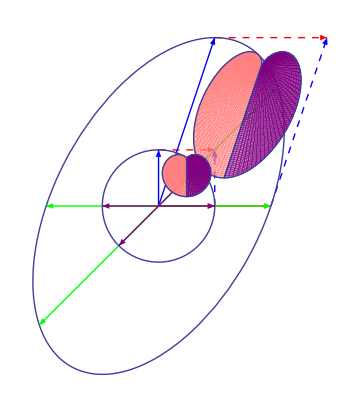
-Graphics- | Matrix | Determinant
(2 | 1
0 | 3) | 6
Eigenvalues | Eigenvectors
3 | (1
1)
2 | (1
0)

```mathematica
InitialA=({{2, 1}, {0, 3}}); 
xrange={0,3}
yrange={0,3}
u=InitialA[[All,1]]
v=InitialA[[All,2]]
box=1
heart=1
Evec=1
circle=1
parabola=0
triangle=0
trianglepoints={{3/4,1/2},{1/4,3/4},{1/4,1/4}}

A=Transpose[{u,v}];
Evals=Eigenvalues[A];
Evecs=Eigenvectors[A];
 Grid[{{Show[Graphics[{ Thick, 
If[triangle==1,{
{GrayLevel[.9],Polygon[trianglepoints]},{GrayLevel[.9],Polygon[trianglepoints.Transpose[A]]},
PointSize[Large],
Point[trianglepoints.Transpose[A]],
Point[trianglepoints]
},Thick],
If[box==1,{
Red, Arrow[{{0, 0}, {1,0}}], {Dashed, Arrow[{{0,1}, {1,1}}]},
Blue, Arrow[{{0, 0}, {0,1}}], {Dashed, Arrow[{{1,0},{1,1}}]},
Red, Arrow[{{0, 0}, u}], {Dashed, Arrow[{v, u + v}]},
Blue, Arrow[{{0, 0}, v}], {Dashed, Arrow[{u, u + v}]}
},Thick],
If[Evec==1,{
Green,Arrow[{{0,0},Evals[[1]]*Normalize[Evecs[[1]]]}],
Green,Arrow[{{0,0},Evals[[2]]*Normalize[Evecs[[2]]]}],
Green,Arrow[{{0,0},-Evals[[1]]*Normalize[Evecs[[1]]]}],
Green,Arrow[{{0,0},-Evals[[2]]*Normalize[Evecs[[2]]]}],
Purple,Arrow[{{0,0},Normalize[Evecs[[1]]]}],
Purple,Arrow[{{0,0},Normalize[Evecs[[2]]]}],
Purple,Arrow[{{0,0},-Normalize[Evecs[[1]]]}],
Purple,Arrow[{{0,0},-Normalize[Evecs[[2]]]}]
},Thick]
}, Axes -> True,ImageSize->Medium],
If[parabola==1,
RegionPlot[Evaluate[(-u[[1]]-y)^2-4(u[[1]]*y-u[[2]]*x)<0],{x,-10,10},{y,-10,10},PlotStyle->Opacity[.1]]
,ParametricPlot[{0,0},{t,0,2Pi}]],
If[circle==1,
{ParametricPlot[A.{Cos[t],Sin[t]},{t,0,2Pi}],
ParametricPlot[{Cos[t],Sin[t]},{t,0,2Pi}]}
,ParametricPlot[{0,0},{t,0,2Pi}]],
If[heart==1,{ParametricPlot[1/3*({(1-Sin[t])*Cos[t],(1-Sin[t])*Sin[t]})*s+{1.5/3,2.5/3},{t,Pi/2,3Pi/2},{s,0,1},PlotStyle->{Pink,Opacity[.5]},Mesh->None],
ParametricPlot[A.(1/3*({(1-Sin[t])*Cos[t],(1-Sin[t])*Sin[t]})*s+{1.5/3,2.5/3}),{t,Pi/2,3Pi/2},{s,0,1},PlotStyle->{Pink,Opacity[.5]},Mesh->None],
ParametricPlot[1/3*({(1-Sin[t])*Cos[t],(1-Sin[t])*Sin[t]})*s+{1.5/3,2.5/3},{t,-Pi/2,Pi/2},{s,0,1},PlotStyle->{Purple,Opacity[.5]},Mesh->None],
ParametricPlot[A.(1/3*({(1-Sin[t])*Cos[t],(1-Sin[t])*Sin[t]})*s+{1.5/3,2.5/3}),{t,-Pi/2,Pi/2},{s,0,1},PlotStyle->{Purple,Opacity[.5]},Mesh->None]}
,ParametricPlot[{0,0},{t,0,2Pi}]],
 PlotRange -> All,Axes->False],
Grid[{{
"Matrix","Determinant"},
{{{Style[A[[1,1]],Red],Style[A[[1,2]],Blue]},{Style[A[[2,1]],Red],Style[A[[2,2]],Blue]}}//MatrixForm,Det[A]},
{"Eigenvalues","Eigenvectors"},
{Evals[[1]],Evecs[[1]]//MatrixForm},
{Evals[[2]],Evecs[[2]]//MatrixForm}
}]}}]
```

{0,3}

{0,3}

{1,-1}

{1,1}

1

1

0

1

0

0

{{3/4,1/2},{1/4,3/4},{1/4,1/4}}

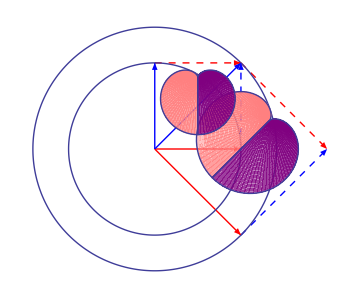
-Graphics- | Matrix | Determinant
(1 | 1
-1 | 1) | 2
Eigenvalues | Eigenvectors
1+ⅈ | (-ⅈ
1)
1-ⅈ | (ⅈ
1)

```mathematica
InitialA=({{1, 1}, {-1, 1}}); 
xrange={0,3}
yrange={0,3}
u=InitialA[[All,1]]
v=InitialA[[All,2]]
box=1
heart=1
Evec=0
circle=1
parabola=0
triangle=0
trianglepoints={{3/4,1/2},{1/4,3/4},{1/4,1/4}}

A=Transpose[{u,v}];
Evals=Eigenvalues[A];
Evecs=Eigenvectors[A];
 Grid[{{Show[Graphics[{ Thick, 
If[triangle==1,{
{GrayLevel[.9],Polygon[trianglepoints]},{GrayLevel[.9],Polygon[trianglepoints.Transpose[A]]},
PointSize[Large],
Point[trianglepoints.Transpose[A]],
Point[trianglepoints]
},Thick],
If[box==1,{
Red, Arrow[{{0, 0}, {1,0}}], {Dashed, Arrow[{{0,1}, {1,1}}]},
Blue, Arrow[{{0, 0}, {0,1}}], {Dashed, Arrow[{{1,0},{1,1}}]},
Red, Arrow[{{0, 0}, u}], {Dashed, Arrow[{v, u + v}]},
Blue, Arrow[{{0, 0}, v}], {Dashed, Arrow[{u, u + v}]}
},Thick],
If[Evec==1,{
Green,Arrow[{{0,0},Evals[[1]]*Normalize[Evecs[[1]]]}],
Green,Arrow[{{0,0},Evals[[2]]*Normalize[Evecs[[2]]]}],
Green,Arrow[{{0,0},-Evals[[1]]*Normalize[Evecs[[1]]]}],
Green,Arrow[{{0,0},-Evals[[2]]*Normalize[Evecs[[2]]]}],
Purple,Arrow[{{0,0},Normalize[Evecs[[1]]]}],
Purple,Arrow[{{0,0},Normalize[Evecs[[2]]]}],
Purple,Arrow[{{0,0},-Normalize[Evecs[[1]]]}],
Purple,Arrow[{{0,0},-Normalize[Evecs[[2]]]}]
},Thick]
}, Axes -> True,ImageSize->Medium],
If[parabola==1,
RegionPlot[Evaluate[(-u[[1]]-y)^2-4(u[[1]]*y-u[[2]]*x)<0],{x,-10,10},{y,-10,10},PlotStyle->Opacity[.1]]
,ParametricPlot[{0,0},{t,0,2Pi}]],
If[circle==1,
{ParametricPlot[A.{Cos[t],Sin[t]},{t,0,2Pi}],
ParametricPlot[{Cos[t],Sin[t]},{t,0,2Pi}]}
,ParametricPlot[{0,0},{t,0,2Pi}]],
If[heart==1,{ParametricPlot[1/3*({(1-Sin[t])*Cos[t],(1-Sin[t])*Sin[t]})*s+{1.5/3,2.5/3},{t,Pi/2,3Pi/2},{s,0,1},PlotStyle->{Pink,Opacity[.5]},Mesh->None],
ParametricPlot[A.(1/3*({(1-Sin[t])*Cos[t],(1-Sin[t])*Sin[t]})*s+{1.5/3,2.5/3}),{t,Pi/2,3Pi/2},{s,0,1},PlotStyle->{Pink,Opacity[.5]},Mesh->None],
ParametricPlot[1/3*({(1-Sin[t])*Cos[t],(1-Sin[t])*Sin[t]})*s+{1.5/3,2.5/3},{t,-Pi/2,Pi/2},{s,0,1},PlotStyle->{Purple,Opacity[.5]},Mesh->None],
ParametricPlot[A.(1/3*({(1-Sin[t])*Cos[t],(1-Sin[t])*Sin[t]})*s+{1.5/3,2.5/3}),{t,-Pi/2,Pi/2},{s,0,1},PlotStyle->{Purple,Opacity[.5]},Mesh->None]}
,ParametricPlot[{0,0},{t,0,2Pi}]],
 PlotRange -> All,Axes->False],
Grid[{{
"Matrix","Determinant"},
{{{Style[A[[1,1]],Red],Style[A[[1,2]],Blue]},{Style[A[[2,1]],Red],Style[A[[2,2]],Blue]}}//MatrixForm,Det[A]},
{"Eigenvalues","Eigenvectors"},
{Evals[[1]],Evecs[[1]]//MatrixForm},
{Evals[[2]],Evecs[[2]]//MatrixForm}
}]}}]
```

{0,3}

{0,3}

{1,1}

{1,-1}

1

1

1

«1 more identical outputs»

0

0

{{3/4,1/2},{1/4,3/4},{1/4,1/4}}

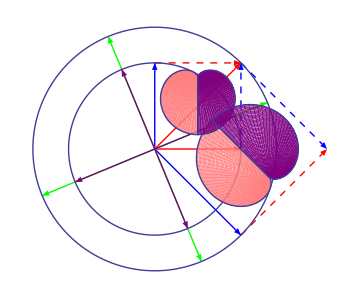
-Graphics- | Matrix | Determinant
(1 | 1
1 | -1) | -2
Eigenvalues | Eigenvectors
-√2 | (1-√2
1)
√2 | (1+√2
1)

```mathematica
InitialA=({{1, 1}, {1, -1}}); 
xrange={0,3}
yrange={0,3}
u=InitialA[[All,1]]
v=InitialA[[All,2]]
box=1
heart=1
Evec=1
circle=1
parabola=0
triangle=0
trianglepoints={{3/4,1/2},{1/4,3/4},{1/4,1/4}}

A=Transpose[{u,v}];
Evals=Eigenvalues[A];
Evecs=Eigenvectors[A];
 Grid[{{Show[Graphics[{ Thick, 
If[triangle==1,{
{GrayLevel[.9],Polygon[trianglepoints]},{GrayLevel[.9],Polygon[trianglepoints.Transpose[A]]},
PointSize[Large],
Point[trianglepoints.Transpose[A]],
Point[trianglepoints]
},Thick],
If[box==1,{
Red, Arrow[{{0, 0}, {1,0}}], {Dashed, Arrow[{{0,1}, {1,1}}]},
Blue, Arrow[{{0, 0}, {0,1}}], {Dashed, Arrow[{{1,0},{1,1}}]},
Red, Arrow[{{0, 0}, u}], {Dashed, Arrow[{v, u + v}]},
Blue, Arrow[{{0, 0}, v}], {Dashed, Arrow[{u, u + v}]}
},Thick],
If[Evec==1,{
Green,Arrow[{{0,0},Evals[[1]]*Normalize[Evecs[[1]]]}],
Green,Arrow[{{0,0},Evals[[2]]*Normalize[Evecs[[2]]]}],
Green,Arrow[{{0,0},-Evals[[1]]*Normalize[Evecs[[1]]]}],
Green,Arrow[{{0,0},-Evals[[2]]*Normalize[Evecs[[2]]]}],
Purple,Arrow[{{0,0},Normalize[Evecs[[1]]]}],
Purple,Arrow[{{0,0},Normalize[Evecs[[2]]]}],
Purple,Arrow[{{0,0},-Normalize[Evecs[[1]]]}],
Purple,Arrow[{{0,0},-Normalize[Evecs[[2]]]}]
},Thick]
}, Axes -> True,ImageSize->Medium],
If[parabola==1,
RegionPlot[Evaluate[(-u[[1]]-y)^2-4(u[[1]]*y-u[[2]]*x)<0],{x,-10,10},{y,-10,10},PlotStyle->Opacity[.1]]
,ParametricPlot[{0,0},{t,0,2Pi}]],
If[circle==1,
{ParametricPlot[A.{Cos[t],Sin[t]},{t,0,2Pi}],
ParametricPlot[{Cos[t],Sin[t]},{t,0,2Pi}]}
,ParametricPlot[{0,0},{t,0,2Pi}]],
If[heart==1,{ParametricPlot[1/3*({(1-Sin[t])*Cos[t],(1-Sin[t])*Sin[t]})*s+{1.5/3,2.5/3},{t,Pi/2,3Pi/2},{s,0,1},PlotStyle->{Pink,Opacity[.5]},Mesh->None],
ParametricPlot[A.(1/3*({(1-Sin[t])*Cos[t],(1-Sin[t])*Sin[t]})*s+{1.5/3,2.5/3}),{t,Pi/2,3Pi/2},{s,0,1},PlotStyle->{Pink,Opacity[.5]},Mesh->None],
ParametricPlot[1/3*({(1-Sin[t])*Cos[t],(1-Sin[t])*Sin[t]})*s+{1.5/3,2.5/3},{t,-Pi/2,Pi/2},{s,0,1},PlotStyle->{Purple,Opacity[.5]},Mesh->None],
ParametricPlot[A.(1/3*({(1-Sin[t])*Cos[t],(1-Sin[t])*Sin[t]})*s+{1.5/3,2.5/3}),{t,-Pi/2,Pi/2},{s,0,1},PlotStyle->{Purple,Opacity[.5]},Mesh->None]}
,ParametricPlot[{0,0},{t,0,2Pi}]],
 PlotRange -> All,Axes->False],
Grid[{{
"Matrix","Determinant"},
{{{Style[A[[1,1]],Red],Style[A[[1,2]],Blue]},{Style[A[[2,1]],Red],Style[A[[2,2]],Blue]}}//MatrixForm,Det[A]},
{"Eigenvalues","Eigenvectors"},
{Evals[[1]],Evecs[[1]]//MatrixForm},
{Evals[[2]],Evecs[[2]]//MatrixForm}
}]}}]
```

{0,3}

{0,3}

{3,1}

{1,3}

1

1

1

«1 more identical outputs»

0

0

{{3/4,1/2},{1/4,3/4},{1/4,1/4}}

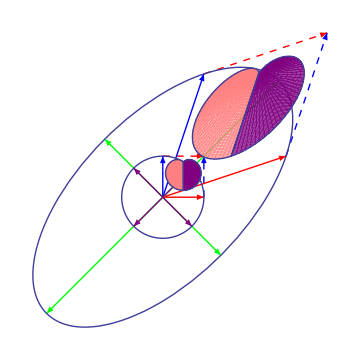
-Graphics- | Matrix | Determinant
(3 | 1
1 | 3) | 8
Eigenvalues | Eigenvectors
4 | (1
1)
2 | (-1
1)

```mathematica
InitialA=({{3, 1}, {1, 3}}); 
xrange={0,3}
yrange={0,3}
u=InitialA[[All,1]]
v=InitialA[[All,2]]
box=1
heart=1
Evec=1
circle=1
parabola=0
triangle=0
trianglepoints={{3/4,1/2},{1/4,3/4},{1/4,1/4}}

A=Transpose[{u,v}];
Evals=Eigenvalues[A];
Evecs=Eigenvectors[A];
 Grid[{{Show[Graphics[{ Thick, 
If[triangle==1,{
{GrayLevel[.9],Polygon[trianglepoints]},{GrayLevel[.9],Polygon[trianglepoints.Transpose[A]]},
PointSize[Large],
Point[trianglepoints.Transpose[A]],
Point[trianglepoints]
},Thick],
If[box==1,{
Red, Arrow[{{0, 0}, {1,0}}], {Dashed, Arrow[{{0,1}, {1,1}}]},
Blue, Arrow[{{0, 0}, {0,1}}], {Dashed, Arrow[{{1,0},{1,1}}]},
Red, Arrow[{{0, 0}, u}], {Dashed, Arrow[{v, u + v}]},
Blue, Arrow[{{0, 0}, v}], {Dashed, Arrow[{u, u + v}]}
},Thick],
If[Evec==1,{
Green,Arrow[{{0,0},Evals[[1]]*Normalize[Evecs[[1]]]}],
Green,Arrow[{{0,0},Evals[[2]]*Normalize[Evecs[[2]]]}],
Green,Arrow[{{0,0},-Evals[[1]]*Normalize[Evecs[[1]]]}],
Green,Arrow[{{0,0},-Evals[[2]]*Normalize[Evecs[[2]]]}],
Purple,Arrow[{{0,0},Normalize[Evecs[[1]]]}],
Purple,Arrow[{{0,0},Normalize[Evecs[[2]]]}],
Purple,Arrow[{{0,0},-Normalize[Evecs[[1]]]}],
Purple,Arrow[{{0,0},-Normalize[Evecs[[2]]]}]
},Thick]
}, Axes -> True,ImageSize->Medium],
If[parabola==1,
RegionPlot[Evaluate[(-u[[1]]-y)^2-4(u[[1]]*y-u[[2]]*x)<0],{x,-10,10},{y,-10,10},PlotStyle->Opacity[.1]]
,ParametricPlot[{0,0},{t,0,2Pi}]],
If[circle==1,
{ParametricPlot[A.{Cos[t],Sin[t]},{t,0,2Pi}],
ParametricPlot[{Cos[t],Sin[t]},{t,0,2Pi}]}
,ParametricPlot[{0,0},{t,0,2Pi}]],
If[heart==1,{ParametricPlot[1/3*({(1-Sin[t])*Cos[t],(1-Sin[t])*Sin[t]})*s+{1.5/3,2.5/3},{t,Pi/2,3Pi/2},{s,0,1},PlotStyle->{Pink,Opacity[.5]},Mesh->None],
ParametricPlot[A.(1/3*({(1-Sin[t])*Cos[t],(1-Sin[t])*Sin[t]})*s+{1.5/3,2.5/3}),{t,Pi/2,3Pi/2},{s,0,1},PlotStyle->{Pink,Opacity[.5]},Mesh->None],
ParametricPlot[1/3*({(1-Sin[t])*Cos[t],(1-Sin[t])*Sin[t]})*s+{1.5/3,2.5/3},{t,-Pi/2,Pi/2},{s,0,1},PlotStyle->{Purple,Opacity[.5]},Mesh->None],
ParametricPlot[A.(1/3*({(1-Sin[t])*Cos[t],(1-Sin[t])*Sin[t]})*s+{1.5/3,2.5/3}),{t,-Pi/2,Pi/2},{s,0,1},PlotStyle->{Purple,Opacity[.5]},Mesh->None]}
,ParametricPlot[{0,0},{t,0,2Pi}]],
 PlotRange -> All,Axes->False],
Grid[{{
"Matrix","Determinant"},
{{{Style[A[[1,1]],Red],Style[A[[1,2]],Blue]},{Style[A[[2,1]],Red],Style[A[[2,2]],Blue]}}//MatrixForm,Det[A]},
{"Eigenvalues","Eigenvectors"},
{Evals[[1]],Evecs[[1]]//MatrixForm},
{Evals[[2]],Evecs[[2]]//MatrixForm}
}]}}]
```

{0,3}

{0,3}

{-1,-3}

{-1,1}

1

1

1

«1 more identical outputs»

0

0

{{3/4,1/2},{1/4,3/4},{1/4,1/4}}

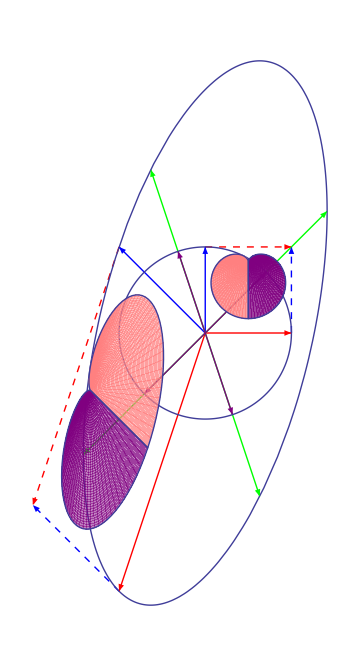
-Graphics- | Matrix | Determinant
(-1 | -1
-3 | 1) | -4
Eigenvalues | Eigenvectors
-2 | (1
1)
2 | (-1
3)

```mathematica
InitialA=({{-1, -1}, {-3, 1}}); 
xrange={0,3}
yrange={0,3}
u=InitialA[[All,1]]
v=InitialA[[All,2]]
box=1
heart=1
Evec=1
circle=1
parabola=0
triangle=0
trianglepoints={{3/4,1/2},{1/4,3/4},{1/4,1/4}}

A=Transpose[{u,v}];
Evals=Eigenvalues[A];
Evecs=Eigenvectors[A];
 Grid[{{Show[Graphics[{ Thick, 
If[triangle==1,{
{GrayLevel[.9],Polygon[trianglepoints]},{GrayLevel[.9],Polygon[trianglepoints.Transpose[A]]},
PointSize[Large],
Point[trianglepoints.Transpose[A]],
Point[trianglepoints]
},Thick],
If[box==1,{
Red, Arrow[{{0, 0}, {1,0}}], {Dashed, Arrow[{{0,1}, {1,1}}]},
Blue, Arrow[{{0, 0}, {0,1}}], {Dashed, Arrow[{{1,0},{1,1}}]},
Red, Arrow[{{0, 0}, u}], {Dashed, Arrow[{v, u + v}]},
Blue, Arrow[{{0, 0}, v}], {Dashed, Arrow[{u, u + v}]}
},Thick],
If[Evec==1,{
Green,Arrow[{{0,0},Evals[[1]]*Normalize[Evecs[[1]]]}],
Green,Arrow[{{0,0},Evals[[2]]*Normalize[Evecs[[2]]]}],
Green,Arrow[{{0,0},-Evals[[1]]*Normalize[Evecs[[1]]]}],
Green,Arrow[{{0,0},-Evals[[2]]*Normalize[Evecs[[2]]]}],
Purple,Arrow[{{0,0},Normalize[Evecs[[1]]]}],
Purple,Arrow[{{0,0},Normalize[Evecs[[2]]]}],
Purple,Arrow[{{0,0},-Normalize[Evecs[[1]]]}],
Purple,Arrow[{{0,0},-Normalize[Evecs[[2]]]}]
},Thick]
}, Axes -> True,ImageSize->Medium],
If[parabola==1,
RegionPlot[Evaluate[(-u[[1]]-y)^2-4(u[[1]]*y-u[[2]]*x)<0],{x,-10,10},{y,-10,10},PlotStyle->Opacity[.1]]
,ParametricPlot[{0,0},{t,0,2Pi}]],
If[circle==1,
{ParametricPlot[A.{Cos[t],Sin[t]},{t,0,2Pi}],
ParametricPlot[{Cos[t],Sin[t]},{t,0,2Pi}]}
,ParametricPlot[{0,0},{t,0,2Pi}]],
If[heart==1,{ParametricPlot[1/3*({(1-Sin[t])*Cos[t],(1-Sin[t])*Sin[t]})*s+{1.5/3,2.5/3},{t,Pi/2,3Pi/2},{s,0,1},PlotStyle->{Pink,Opacity[.5]},Mesh->None],
ParametricPlot[A.(1/3*({(1-Sin[t])*Cos[t],(1-Sin[t])*Sin[t]})*s+{1.5/3,2.5/3}),{t,Pi/2,3Pi/2},{s,0,1},PlotStyle->{Pink,Opacity[.5]},Mesh->None],
ParametricPlot[1/3*({(1-Sin[t])*Cos[t],(1-Sin[t])*Sin[t]})*s+{1.5/3,2.5/3},{t,-Pi/2,Pi/2},{s,0,1},PlotStyle->{Purple,Opacity[.5]},Mesh->None],
ParametricPlot[A.(1/3*({(1-Sin[t])*Cos[t],(1-Sin[t])*Sin[t]})*s+{1.5/3,2.5/3}),{t,-Pi/2,Pi/2},{s,0,1},PlotStyle->{Purple,Opacity[.5]},Mesh->None]}
,ParametricPlot[{0,0},{t,0,2Pi}]],
 PlotRange -> All,Axes->False],
Grid[{{
"Matrix","Determinant"},
{{{Style[A[[1,1]],Red],Style[A[[1,2]],Blue]},{Style[A[[2,1]],Red],Style[A[[2,2]],Blue]}}//MatrixForm,Det[A]},
{"Eigenvalues","Eigenvectors"},
{Evals[[1]],Evecs[[1]]//MatrixForm},
{Evals[[2]],Evecs[[2]]//MatrixForm}
}]}}]
```

{0,3}

{0,3}

{1,-1}

{1,1}

1

0

0

0

«1 more identical outputs»

1

{{3/4,1/2},{1/4,3/4},{1/4,1/4}}

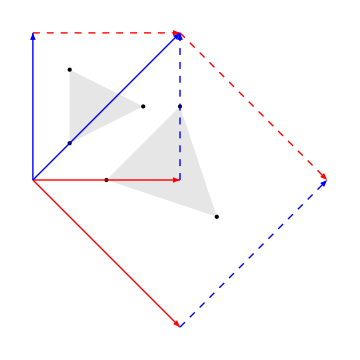
-Graphics- | Matrix | Determinant
(1 | 1
-1 | 1) | 2
Eigenvalues | Eigenvectors
1+ⅈ | (-ⅈ
1)
1-ⅈ | (ⅈ
1)

```mathematica
InitialA=({{1, 1}, {-1, 1}}); 
xrange={0,3}
yrange={0,3}
u=InitialA[[All,1]]
v=InitialA[[All,2]]
box=1
heart=0
Evec=0
circle=0
parabola=0
triangle=1
trianglepoints={{3/4,1/2},{1/4,3/4},{1/4,1/4}}

A=Transpose[{u,v}];
Evals=Eigenvalues[A];
Evecs=Eigenvectors[A];
 Grid[{{Show[Graphics[{ Thick, 
If[triangle==1,{
{GrayLevel[.9],Polygon[trianglepoints]},{GrayLevel[.9],Polygon[trianglepoints.Transpose[A]]},
PointSize[Large],
Point[trianglepoints.Transpose[A]],
Point[trianglepoints]
},Thick],
If[box==1,{
Red, Arrow[{{0, 0}, {1,0}}], {Dashed, Arrow[{{0,1}, {1,1}}]},
Blue, Arrow[{{0, 0}, {0,1}}], {Dashed, Arrow[{{1,0},{1,1}}]},
Red, Arrow[{{0, 0}, u}], {Dashed, Arrow[{v, u + v}]},
Blue, Arrow[{{0, 0}, v}], {Dashed, Arrow[{u, u + v}]}
},Thick],
If[Evec==1,{
Green,Arrow[{{0,0},Evals[[1]]*Normalize[Evecs[[1]]]}],
Green,Arrow[{{0,0},Evals[[2]]*Normalize[Evecs[[2]]]}],
Green,Arrow[{{0,0},-Evals[[1]]*Normalize[Evecs[[1]]]}],
Green,Arrow[{{0,0},-Evals[[2]]*Normalize[Evecs[[2]]]}],
Purple,Arrow[{{0,0},Normalize[Evecs[[1]]]}],
Purple,Arrow[{{0,0},Normalize[Evecs[[2]]]}],
Purple,Arrow[{{0,0},-Normalize[Evecs[[1]]]}],
Purple,Arrow[{{0,0},-Normalize[Evecs[[2]]]}]
},Thick]
}, Axes -> True,ImageSize->Medium],
If[parabola==1,
RegionPlot[Evaluate[(-u[[1]]-y)^2-4(u[[1]]*y-u[[2]]*x)<0],{x,-10,10},{y,-10,10},PlotStyle->Opacity[.1]]
,ParametricPlot[{0,0},{t,0,2Pi}]],
If[circle==1,
{ParametricPlot[A.{Cos[t],Sin[t]},{t,0,2Pi}],
ParametricPlot[{Cos[t],Sin[t]},{t,0,2Pi}]}
,ParametricPlot[{0,0},{t,0,2Pi}]],
If[heart==1,{ParametricPlot[1/3*({(1-Sin[t])*Cos[t],(1-Sin[t])*Sin[t]})*s+{1.5/3,2.5/3},{t,Pi/2,3Pi/2},{s,0,1},PlotStyle->{Pink,Opacity[.5]},Mesh->None],
ParametricPlot[A.(1/3*({(1-Sin[t])*Cos[t],(1-Sin[t])*Sin[t]})*s+{1.5/3,2.5/3}),{t,Pi/2,3Pi/2},{s,0,1},PlotStyle->{Pink,Opacity[.5]},Mesh->None],
ParametricPlot[1/3*({(1-Sin[t])*Cos[t],(1-Sin[t])*Sin[t]})*s+{1.5/3,2.5/3},{t,-Pi/2,Pi/2},{s,0,1},PlotStyle->{Purple,Opacity[.5]},Mesh->None],
ParametricPlot[A.(1/3*({(1-Sin[t])*Cos[t],(1-Sin[t])*Sin[t]})*s+{1.5/3,2.5/3}),{t,-Pi/2,Pi/2},{s,0,1},PlotStyle->{Purple,Opacity[.5]},Mesh->None]}
,ParametricPlot[{0,0},{t,0,2Pi}]],
 PlotRange -> All,Axes->False],
Grid[{{
"Matrix","Determinant"},
{{{Style[A[[1,1]],Red],Style[A[[1,2]],Blue]},{Style[A[[2,1]],Red],Style[A[[2,2]],Blue]}}//MatrixForm,Det[A]},
{"Eigenvalues","Eigenvectors"},
{Evals[[1]],Evecs[[1]]//MatrixForm},
{Evals[[2]],Evecs[[2]]//MatrixForm}
}]}}]
```

{0,3}

{0,3}

{1,1}

{1,-1}

1

0

0

0

«1 more identical outputs»

1

{{3/4,1/2},{1/4,3/4},{1/4,1/4}}

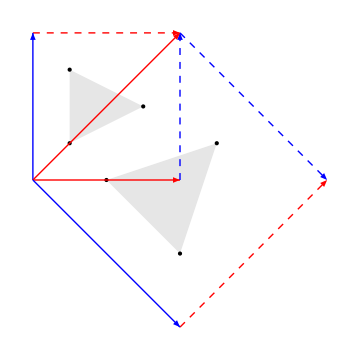
-Graphics- | Matrix | Determinant
(1 | 1
1 | -1) | -2
Eigenvalues | Eigenvectors
-√2 | (1-√2
1)
√2 | (1+√2
1)

```mathematica
InitialA=({{1, 1}, {1, -1}}); 
xrange={0,3}
yrange={0,3}
u=InitialA[[All,1]]
v=InitialA[[All,2]]
box=1
heart=0
Evec=0
circle=0
parabola=0
triangle=1
trianglepoints={{3/4,1/2},{1/4,3/4},{1/4,1/4}}

A=Transpose[{u,v}];
Evals=Eigenvalues[A];
Evecs=Eigenvectors[A];
 Grid[{{Show[Graphics[{ Thick, 
If[triangle==1,{
{GrayLevel[.9],Polygon[trianglepoints]},{GrayLevel[.9],Polygon[trianglepoints.Transpose[A]]},
PointSize[Large],
Point[trianglepoints.Transpose[A]],
Point[trianglepoints]
},Thick],
If[box==1,{
Red, Arrow[{{0, 0}, {1,0}}], {Dashed, Arrow[{{0,1}, {1,1}}]},
Blue, Arrow[{{0, 0}, {0,1}}], {Dashed, Arrow[{{1,0},{1,1}}]},
Red, Arrow[{{0, 0}, u}], {Dashed, Arrow[{v, u + v}]},
Blue, Arrow[{{0, 0}, v}], {Dashed, Arrow[{u, u + v}]}
},Thick],
If[Evec==1,{
Green,Arrow[{{0,0},Evals[[1]]*Normalize[Evecs[[1]]]}],
Green,Arrow[{{0,0},Evals[[2]]*Normalize[Evecs[[2]]]}],
Green,Arrow[{{0,0},-Evals[[1]]*Normalize[Evecs[[1]]]}],
Green,Arrow[{{0,0},-Evals[[2]]*Normalize[Evecs[[2]]]}],
Purple,Arrow[{{0,0},Normalize[Evecs[[1]]]}],
Purple,Arrow[{{0,0},Normalize[Evecs[[2]]]}],
Purple,Arrow[{{0,0},-Normalize[Evecs[[1]]]}],
Purple,Arrow[{{0,0},-Normalize[Evecs[[2]]]}]
},Thick]
}, Axes -> True,ImageSize->Medium],
If[parabola==1,
RegionPlot[Evaluate[(-u[[1]]-y)^2-4(u[[1]]*y-u[[2]]*x)<0],{x,-10,10},{y,-10,10},PlotStyle->Opacity[.1]]
,ParametricPlot[{0,0},{t,0,2Pi}]],
If[circle==1,
{ParametricPlot[A.{Cos[t],Sin[t]},{t,0,2Pi}],
ParametricPlot[{Cos[t],Sin[t]},{t,0,2Pi}]}
,ParametricPlot[{0,0},{t,0,2Pi}]],
If[heart==1,{ParametricPlot[1/3*({(1-Sin[t])*Cos[t],(1-Sin[t])*Sin[t]})*s+{1.5/3,2.5/3},{t,Pi/2,3Pi/2},{s,0,1},PlotStyle->{Pink,Opacity[.5]},Mesh->None],
ParametricPlot[A.(1/3*({(1-Sin[t])*Cos[t],(1-Sin[t])*Sin[t]})*s+{1.5/3,2.5/3}),{t,Pi/2,3Pi/2},{s,0,1},PlotStyle->{Pink,Opacity[.5]},Mesh->None],
ParametricPlot[1/3*({(1-Sin[t])*Cos[t],(1-Sin[t])*Sin[t]})*s+{1.5/3,2.5/3},{t,-Pi/2,Pi/2},{s,0,1},PlotStyle->{Purple,Opacity[.5]},Mesh->None],
ParametricPlot[A.(1/3*({(1-Sin[t])*Cos[t],(1-Sin[t])*Sin[t]})*s+{1.5/3,2.5/3}),{t,-Pi/2,Pi/2},{s,0,1},PlotStyle->{Purple,Opacity[.5]},Mesh->None]}
,ParametricPlot[{0,0},{t,0,2Pi}]],
 PlotRange -> All,Axes->False],
Grid[{{
"Matrix","Determinant"},
{{{Style[A[[1,1]],Red],Style[A[[1,2]],Blue]},{Style[A[[2,1]],Red],Style[A[[2,2]],Blue]}}//MatrixForm,Det[A]},
{"Eigenvalues","Eigenvectors"},
{Evals[[1]],Evecs[[1]]//MatrixForm},
{Evals[[2]],Evecs[[2]]//MatrixForm}
}]}}]
```

{0,3}

{0,3}

{3,1}

{1,3}

1

0

0

0

«1 more identical outputs»

1

{{3/4,1/2},{1/4,3/4},{1/4,1/4}}

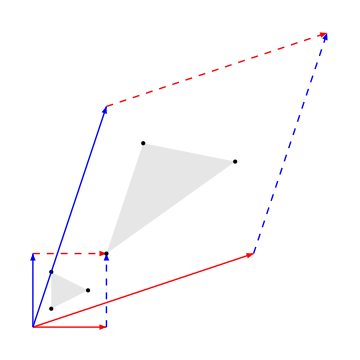
-Graphics- | Matrix | Determinant
(3 | 1
1 | 3) | 8
Eigenvalues | Eigenvectors
4 | (1
1)
2 | (-1
1)

```mathematica
InitialA=({{3, 1}, {1, 3}}); 
xrange={0,3}
yrange={0,3}
u=InitialA[[All,1]]
v=InitialA[[All,2]]
box=1
heart=0
Evec=0
circle=0
parabola=0
triangle=1
trianglepoints={{3/4,1/2},{1/4,3/4},{1/4,1/4}}

A=Transpose[{u,v}];
Evals=Eigenvalues[A];
Evecs=Eigenvectors[A];
 Grid[{{Show[Graphics[{ Thick, 
If[triangle==1,{
{GrayLevel[.9],Polygon[trianglepoints]},{GrayLevel[.9],Polygon[trianglepoints.Transpose[A]]},
PointSize[Large],
Point[trianglepoints.Transpose[A]],
Point[trianglepoints]
},Thick],
If[box==1,{
Red, Arrow[{{0, 0}, {1,0}}], {Dashed, Arrow[{{0,1}, {1,1}}]},
Blue, Arrow[{{0, 0}, {0,1}}], {Dashed, Arrow[{{1,0},{1,1}}]},
Red, Arrow[{{0, 0}, u}], {Dashed, Arrow[{v, u + v}]},
Blue, Arrow[{{0, 0}, v}], {Dashed, Arrow[{u, u + v}]}
},Thick],
If[Evec==1,{
Green,Arrow[{{0,0},Evals[[1]]*Normalize[Evecs[[1]]]}],
Green,Arrow[{{0,0},Evals[[2]]*Normalize[Evecs[[2]]]}],
Green,Arrow[{{0,0},-Evals[[1]]*Normalize[Evecs[[1]]]}],
Green,Arrow[{{0,0},-Evals[[2]]*Normalize[Evecs[[2]]]}],
Purple,Arrow[{{0,0},Normalize[Evecs[[1]]]}],
Purple,Arrow[{{0,0},Normalize[Evecs[[2]]]}],
Purple,Arrow[{{0,0},-Normalize[Evecs[[1]]]}],
Purple,Arrow[{{0,0},-Normalize[Evecs[[2]]]}]
},Thick]
}, Axes -> True,ImageSize->Medium],
If[parabola==1,
RegionPlot[Evaluate[(-u[[1]]-y)^2-4(u[[1]]*y-u[[2]]*x)<0],{x,-10,10},{y,-10,10},PlotStyle->Opacity[.1]]
,ParametricPlot[{0,0},{t,0,2Pi}]],
If[circle==1,
{ParametricPlot[A.{Cos[t],Sin[t]},{t,0,2Pi}],
ParametricPlot[{Cos[t],Sin[t]},{t,0,2Pi}]}
,ParametricPlot[{0,0},{t,0,2Pi}]],
If[heart==1,{ParametricPlot[1/3*({(1-Sin[t])*Cos[t],(1-Sin[t])*Sin[t]})*s+{1.5/3,2.5/3},{t,Pi/2,3Pi/2},{s,0,1},PlotStyle->{Pink,Opacity[.5]},Mesh->None],
ParametricPlot[A.(1/3*({(1-Sin[t])*Cos[t],(1-Sin[t])*Sin[t]})*s+{1.5/3,2.5/3}),{t,Pi/2,3Pi/2},{s,0,1},PlotStyle->{Pink,Opacity[.5]},Mesh->None],
ParametricPlot[1/3*({(1-Sin[t])*Cos[t],(1-Sin[t])*Sin[t]})*s+{1.5/3,2.5/3},{t,-Pi/2,Pi/2},{s,0,1},PlotStyle->{Purple,Opacity[.5]},Mesh->None],
ParametricPlot[A.(1/3*({(1-Sin[t])*Cos[t],(1-Sin[t])*Sin[t]})*s+{1.5/3,2.5/3}),{t,-Pi/2,Pi/2},{s,0,1},PlotStyle->{Purple,Opacity[.5]},Mesh->None]}
,ParametricPlot[{0,0},{t,0,2Pi}]],
 PlotRange -> All,Axes->False],
Grid[{{
"Matrix","Determinant"},
{{{Style[A[[1,1]],Red],Style[A[[1,2]],Blue]},{Style[A[[2,1]],Red],Style[A[[2,2]],Blue]}}//MatrixForm,Det[A]},
{"Eigenvalues","Eigenvectors"},
{Evals[[1]],Evecs[[1]]//MatrixForm},
{Evals[[2]],Evecs[[2]]//MatrixForm}
}]}}]
```

{0,3}

{0,3}

{-1,-3}

{-1,1}

1

0

0

0

«1 more identical outputs»

1

{{3/4,1/2},{1/4,3/4},{1/4,1/4}}

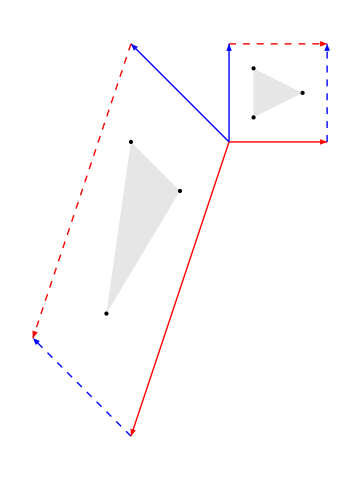
-Graphics- | Matrix | Determinant
(-1 | -1
-3 | 1) | -4
Eigenvalues | Eigenvectors
-2 | (1
1)
2 | (-1
3)

```mathematica
InitialA=({{-1, -1}, {-3, 1}}); 
xrange={0,3}
yrange={0,3}
u=InitialA[[All,1]]
v=InitialA[[All,2]]
box=1
heart=0
Evec=0
circle=0
parabola=0
triangle=1
trianglepoints={{3/4,1/2},{1/4,3/4},{1/4,1/4}}

A=Transpose[{u,v}];
Evals=Eigenvalues[A];
Evecs=Eigenvectors[A];
 Grid[{{Show[Graphics[{ Thick, 
If[triangle==1,{
{GrayLevel[.9],Polygon[trianglepoints]},{GrayLevel[.9],Polygon[trianglepoints.Transpose[A]]},
PointSize[Large],
Point[trianglepoints.Transpose[A]],
Point[trianglepoints]
},Thick],
If[box==1,{
Red, Arrow[{{0, 0}, {1,0}}], {Dashed, Arrow[{{0,1}, {1,1}}]},
Blue, Arrow[{{0, 0}, {0,1}}], {Dashed, Arrow[{{1,0},{1,1}}]},
Red, Arrow[{{0, 0}, u}], {Dashed, Arrow[{v, u + v}]},
Blue, Arrow[{{0, 0}, v}], {Dashed, Arrow[{u, u + v}]}
},Thick],
If[Evec==1,{
Green,Arrow[{{0,0},Evals[[1]]*Normalize[Evecs[[1]]]}],
Green,Arrow[{{0,0},Evals[[2]]*Normalize[Evecs[[2]]]}],
Green,Arrow[{{0,0},-Evals[[1]]*Normalize[Evecs[[1]]]}],
Green,Arrow[{{0,0},-Evals[[2]]*Normalize[Evecs[[2]]]}],
Purple,Arrow[{{0,0},Normalize[Evecs[[1]]]}],
Purple,Arrow[{{0,0},Normalize[Evecs[[2]]]}],
Purple,Arrow[{{0,0},-Normalize[Evecs[[1]]]}],
Purple,Arrow[{{0,0},-Normalize[Evecs[[2]]]}]
},Thick]
}, Axes -> True,ImageSize->Medium],
If[parabola==1,
RegionPlot[Evaluate[(-u[[1]]-y)^2-4(u[[1]]*y-u[[2]]*x)<0],{x,-10,10},{y,-10,10},PlotStyle->Opacity[.1]]
,ParametricPlot[{0,0},{t,0,2Pi}]],
If[circle==1,
{ParametricPlot[A.{Cos[t],Sin[t]},{t,0,2Pi}],
ParametricPlot[{Cos[t],Sin[t]},{t,0,2Pi}]}
,ParametricPlot[{0,0},{t,0,2Pi}]],
If[heart==1,{ParametricPlot[1/3*({(1-Sin[t])*Cos[t],(1-Sin[t])*Sin[t]})*s+{1.5/3,2.5/3},{t,Pi/2,3Pi/2},{s,0,1},PlotStyle->{Pink,Opacity[.5]},Mesh->None],
ParametricPlot[A.(1/3*({(1-Sin[t])*Cos[t],(1-Sin[t])*Sin[t]})*s+{1.5/3,2.5/3}),{t,Pi/2,3Pi/2},{s,0,1},PlotStyle->{Pink,Opacity[.5]},Mesh->None],
ParametricPlot[1/3*({(1-Sin[t])*Cos[t],(1-Sin[t])*Sin[t]})*s+{1.5/3,2.5/3},{t,-Pi/2,Pi/2},{s,0,1},PlotStyle->{Purple,Opacity[.5]},Mesh->None],
ParametricPlot[A.(1/3*({(1-Sin[t])*Cos[t],(1-Sin[t])*Sin[t]})*s+{1.5/3,2.5/3}),{t,-Pi/2,Pi/2},{s,0,1},PlotStyle->{Purple,Opacity[.5]},Mesh->None]}
,ParametricPlot[{0,0},{t,0,2Pi}]],
 PlotRange -> All,Axes->False],
Grid[{{
"Matrix","Determinant"},
{{{Style[A[[1,1]],Red],Style[A[[1,2]],Blue]},{Style[A[[2,1]],Red],Style[A[[2,2]],Blue]}}//MatrixForm,Det[A]},
{"Eigenvalues","Eigenvectors"},
{Evals[[1]],Evecs[[1]]//MatrixForm},
{Evals[[2]],Evecs[[2]]//MatrixForm}
}]}}]
```

### 3D Transformations

```mathematica
box=1
eigenvectors=0
sphere=0
flower=1

A=({{2, 0, 0}, {1, 2, 1}, {0, 1, 2}});


u=A[[All,1]];
v=A[[All,2]];
w=A[[All,3]];

Evals=Eigenvalues[A];
Evecs=Eigenvectors[A]; 

ev1=Normalize[Evecs[[1]]];
ev2=Normalize[Evecs[[2]]];
ev3=Normalize[Evecs[[3]]];

z={0,0,0};
e1={1,0,0};
e2={0,1,0};
e3={0,0,1};

boxp=Show[{ Graphics3D[{ 
Thick, Red, Arrow[{z,e1}], {Dashed, Arrow[{e2, e2+e1}],Arrow[{e3, e3+e1}]},
Green, Arrow[{z,e2}], {Dashed, Arrow[{e1, e1+e2}],Arrow[{e3, e3+e2}]},
Blue, Arrow[{z,e3}], {Dashed, Arrow[{e1, e1+e3}],Arrow[{e2, e2+e3}]},
Red, Arrow[{z,u}], {Dashed, Arrow[{v, v+u}],Arrow[{w, w+u}]},
Green, Arrow[{z,v}], {Dashed, Arrow[{u, u+v}],Arrow[{w, w+v}]},
Blue, Arrow[{z,w}], {Dashed, Arrow[{u, u+w}],Arrow[{v, v+w}]}
}],
ParametricPlot3D[s*e1+t*e2,{s,0,1},{t,0,1},PlotStyle->{RGBColor[1,1,0],Opacity[.2]},Mesh->{1,1},MeshStyle->{Green,Red},MeshStyle->Opacity[.2]],
ParametricPlot3D[s*e1+t*e3,{s,0,1},{t,0,1},PlotStyle->{RGBColor[1,0,1],Opacity[.2]},Mesh->{1,1},MeshStyle->{Blue,Red},MeshStyle->Opacity[.2]],
ParametricPlot3D[s*e2+t*e3,{s,0,1},{t,0,1},PlotStyle->{RGBColor[0,1,1],Opacity[.2]},Mesh->{1,1},MeshStyle->{Blue,Green},MeshStyle->Opacity[.2]],

ParametricPlot3D[s*u+t*v,{s,0,1},{t,0,1},PlotStyle->{RGBColor[1,1,0],Opacity[.2]},Mesh->{1,1},MeshStyle->{Green,Red},MeshStyle->Opacity[.2]],
ParametricPlot3D[s*u+t*w,{s,0,1},{t,0,1},PlotStyle->{RGBColor[1,0,1],Opacity[.2]},Mesh->{1,1},MeshStyle->{Blue,Red},MeshStyle->Opacity[.2]],
ParametricPlot3D[s*v+t*w,{s,0,1},{t,0,1},PlotStyle->{RGBColor[0,1,1],Opacity[.2]},Mesh->{1,1},MeshStyle->{Blue,Green},MeshStyle->Opacity[.2]]
}];

evecp=Graphics3D[{ 
Thick, Black, 
Arrow[{z,ev1}],
Arrow[{z,ev2}],
Arrow[{z,ev3}],
Thick, Purple, 
Arrow[{z,Evals[[1]]*ev1}],
Arrow[{z,Evals[[2]]*ev2}],
Arrow[{z,Evals[[3]]*ev3}]
}];

p=ParametricPlot3D[1/2{Cos[t]Cos[s]Sin[3s],Sin[t]Cos[s]Sin[3s],Sin[s]Sin[3s]}+{1/2,1/2,1/2},{s,0,Pi},{t,0,2Pi},PerformanceGoal->"Speed",PlotStyle->Opacity[.5]];
Ap=ParametricPlot3D[A.(1/2{Cos[t]Cos[s]Sin[3s],Sin[t]Cos[s]Sin[3s],Sin[s]Sin[3s]}+{1/2,1/2,1/2}),{s,0,Pi},{t,0,2Pi},PerformanceGoal->"Speed",PlotStyle->Opacity[.5]];
sp=ParametricPlot3D[{Cos[t]Sin[s],Sin[t]Sin[s],Cos[s]},{s,0,Pi},{t,0,2Pi},PlotStyle->None,MeshStyle->Opacity[.2]];
Asp=ParametricPlot3D[A.{Cos[t]Sin[s],Sin[t]Sin[s],Cos[s]},{s,0,Pi},{t,0,2Pi},PlotStyle->None,MeshStyle->Opacity[.2]];


Grid[{{Show[{
If[box==1,boxp,Graphics3D[Point[{z}]]],
If[eigenvectors==1,evecp,Graphics3D[Point[{z}]]],
If[sphere==1,{sp,Asp},Graphics3D[Point[{z}]]],
If[flower==1,{p,Ap},Graphics3D[Point[{z}]]]
},Axes->True,AxesLabel->{"x","y","z"},ImageSize->Medium],
Grid[({{"Matrix", "Determinant"}, {A//MatrixForm, Det[A]}, {"Eigenvalue", "Eigenvector"}, {Evals[[1]], Evecs[[1]]//MatrixForm}, {Evals[[2]], Evecs[[2]]//MatrixForm}, {Evals[[3]], Evecs[[3]]//MatrixForm}})]}}]
```

1

0

0

1

-Graphics3D- | Matrix | Determinant
(2 | 0 | 0
1 | 2 | 1
0 | 1 | 2) | 6
Eigenvalue | Eigenvector
3 | (0
1
1)
2 | (-1
0
1)
1 | (0
-1
1)

```mathematica
box=1
eigenvectors=1
sphere=1
flower=0

A=({{2, 0, 0}, {1, 2, 1}, {0, 1, 2}});


u=A[[All,1]];
v=A[[All,2]];
w=A[[All,3]];

Evals=Eigenvalues[A];
Evecs=Eigenvectors[A]; 

ev1=Normalize[Evecs[[1]]];
ev2=Normalize[Evecs[[2]]];
ev3=Normalize[Evecs[[3]]];

z={0,0,0};
e1={1,0,0};
e2={0,1,0};
e3={0,0,1};

boxp=Show[{ Graphics3D[{ 
Thick, Red, Arrow[{z,e1}], {Dashed, Arrow[{e2, e2+e1}],Arrow[{e3, e3+e1}]},
Green, Arrow[{z,e2}], {Dashed, Arrow[{e1, e1+e2}],Arrow[{e3, e3+e2}]},
Blue, Arrow[{z,e3}], {Dashed, Arrow[{e1, e1+e3}],Arrow[{e2, e2+e3}]},
Red, Arrow[{z,u}], {Dashed, Arrow[{v, v+u}],Arrow[{w, w+u}]},
Green, Arrow[{z,v}], {Dashed, Arrow[{u, u+v}],Arrow[{w, w+v}]},
Blue, Arrow[{z,w}], {Dashed, Arrow[{u, u+w}],Arrow[{v, v+w}]}
}],
ParametricPlot3D[s*e1+t*e2,{s,0,1},{t,0,1},PlotStyle->{RGBColor[1,1,0],Opacity[.2]},Mesh->{1,1},MeshStyle->{Green,Red},MeshStyle->Opacity[.2]],
ParametricPlot3D[s*e1+t*e3,{s,0,1},{t,0,1},PlotStyle->{RGBColor[1,0,1],Opacity[.2]},Mesh->{1,1},MeshStyle->{Blue,Red},MeshStyle->Opacity[.2]],
ParametricPlot3D[s*e2+t*e3,{s,0,1},{t,0,1},PlotStyle->{RGBColor[0,1,1],Opacity[.2]},Mesh->{1,1},MeshStyle->{Blue,Green},MeshStyle->Opacity[.2]],

ParametricPlot3D[s*u+t*v,{s,0,1},{t,0,1},PlotStyle->{RGBColor[1,1,0],Opacity[.2]},Mesh->{1,1},MeshStyle->{Green,Red},MeshStyle->Opacity[.2]],
ParametricPlot3D[s*u+t*w,{s,0,1},{t,0,1},PlotStyle->{RGBColor[1,0,1],Opacity[.2]},Mesh->{1,1},MeshStyle->{Blue,Red},MeshStyle->Opacity[.2]],
ParametricPlot3D[s*v+t*w,{s,0,1},{t,0,1},PlotStyle->{RGBColor[0,1,1],Opacity[.2]},Mesh->{1,1},MeshStyle->{Blue,Green},MeshStyle->Opacity[.2]]
}];

evecp=Graphics3D[{ 
Thick, Black, 
Arrow[{z,ev1}],
Arrow[{z,ev2}],
Arrow[{z,ev3}],
Thick, Purple, 
Arrow[{z,Evals[[1]]*ev1}],
Arrow[{z,Evals[[2]]*ev2}],
Arrow[{z,Evals[[3]]*ev3}]
}];

p=ParametricPlot3D[1/2{Cos[t]Cos[s]Sin[3s],Sin[t]Cos[s]Sin[3s],Sin[s]Sin[3s]}+{1/2,1/2,1/2},{s,0,Pi},{t,0,2Pi},PerformanceGoal->"Speed",PlotStyle->Opacity[.5]];
Ap=ParametricPlot3D[A.(1/2{Cos[t]Cos[s]Sin[3s],Sin[t]Cos[s]Sin[3s],Sin[s]Sin[3s]}+{1/2,1/2,1/2}),{s,0,Pi},{t,0,2Pi},PerformanceGoal->"Speed",PlotStyle->Opacity[.5]];
sp=ParametricPlot3D[{Cos[t]Sin[s],Sin[t]Sin[s],Cos[s]},{s,0,Pi},{t,0,2Pi},PlotStyle->None,MeshStyle->Opacity[.2]];
Asp=ParametricPlot3D[A.{Cos[t]Sin[s],Sin[t]Sin[s],Cos[s]},{s,0,Pi},{t,0,2Pi},PlotStyle->None,MeshStyle->Opacity[.2]];


Grid[{{Show[{
If[box==1,boxp,Graphics3D[Point[{z}]]],
If[eigenvectors==1,evecp,Graphics3D[Point[{z}]]],
If[sphere==1,{sp,Asp},Graphics3D[Point[{z}]]],
If[flower==1,{p,Ap},Graphics3D[Point[{z}]]]
},Axes->True,AxesLabel->{"x","y","z"},ImageSize->Medium],
Grid[({{"Matrix", "Determinant"}, {A//MatrixForm, Det[A]}, {"Eigenvalue", "Eigenvector"}, {Evals[[1]], Evecs[[1]]//MatrixForm}, {Evals[[2]], Evecs[[2]]//MatrixForm}, {Evals[[3]], Evecs[[3]]//MatrixForm}})]}}]
```

1

1

1

0

-Graphics3D- | Matrix | Determinant
(2 | 0 | 0
1 | 2 | 1
0 | 1 | 2) | 6
Eigenvalue | Eigenvector
3 | (0
1
1)
2 | (-1
0
1)
1 | (0
-1
1)

```mathematica
TeXForm[A]
```

\left(
\begin{array}{ccc}
 2 & 0 & 0 \\
 1 & 2 & 1 \\
 0 & 1 & 2
\end{array}
\right)

```mathematica
box=1
eigenvectors=0
sphere=0
flower=1
A=({{0, 0, -1}, {0, -3, 0}, {-2, 0, 0}});



u=A[[All,1]];
v=A[[All,2]];
w=A[[All,3]];

Evals=Eigenvalues[A];
Evecs=Eigenvectors[A]; 

ev1=Normalize[Evecs[[1]]];
ev2=Normalize[Evecs[[2]]];
ev3=Normalize[Evecs[[3]]];

z={0,0,0};
e1={1,0,0};
e2={0,1,0};
e3={0,0,1};

boxp=Show[{ Graphics3D[{ 
Thick, Red, Arrow[{z,e1}], {Dashed, Arrow[{e2, e2+e1}],Arrow[{e3, e3+e1}]},
Green, Arrow[{z,e2}], {Dashed, Arrow[{e1, e1+e2}],Arrow[{e3, e3+e2}]},
Blue, Arrow[{z,e3}], {Dashed, Arrow[{e1, e1+e3}],Arrow[{e2, e2+e3}]},
Red, Arrow[{z,u}], {Dashed, Arrow[{v, v+u}],Arrow[{w, w+u}]},
Green, Arrow[{z,v}], {Dashed, Arrow[{u, u+v}],Arrow[{w, w+v}]},
Blue, Arrow[{z,w}], {Dashed, Arrow[{u, u+w}],Arrow[{v, v+w}]}
}],
ParametricPlot3D[s*e1+t*e2,{s,0,1},{t,0,1},PlotStyle->{RGBColor[1,1,0],Opacity[.2]},Mesh->{1,1},MeshStyle->{Green,Red},MeshStyle->Opacity[.2]],
ParametricPlot3D[s*e1+t*e3,{s,0,1},{t,0,1},PlotStyle->{RGBColor[1,0,1],Opacity[.2]},Mesh->{1,1},MeshStyle->{Blue,Red},MeshStyle->Opacity[.2]],
ParametricPlot3D[s*e2+t*e3,{s,0,1},{t,0,1},PlotStyle->{RGBColor[0,1,1],Opacity[.2]},Mesh->{1,1},MeshStyle->{Blue,Green},MeshStyle->Opacity[.2]],

ParametricPlot3D[s*u+t*v,{s,0,1},{t,0,1},PlotStyle->{RGBColor[1,1,0],Opacity[.2]},Mesh->{1,1},MeshStyle->{Green,Red},MeshStyle->Opacity[.2]],
ParametricPlot3D[s*u+t*w,{s,0,1},{t,0,1},PlotStyle->{RGBColor[1,0,1],Opacity[.2]},Mesh->{1,1},MeshStyle->{Blue,Red},MeshStyle->Opacity[.2]],
ParametricPlot3D[s*v+t*w,{s,0,1},{t,0,1},PlotStyle->{RGBColor[0,1,1],Opacity[.2]},Mesh->{1,1},MeshStyle->{Blue,Green},MeshStyle->Opacity[.2]]
}];

evecp=Graphics3D[{ 
Thick, Black, 
Arrow[{z,ev1}],
Arrow[{z,ev2}],
Arrow[{z,ev3}],
Thick, Purple, 
Arrow[{z,Evals[[1]]*ev1}],
Arrow[{z,Evals[[2]]*ev2}],
Arrow[{z,Evals[[3]]*ev3}]
}];

p=ParametricPlot3D[1/2{Cos[t]Cos[s]Sin[3s],Sin[t]Cos[s]Sin[3s],Sin[s]Sin[3s]}+{1/2,1/2,1/2},{s,0,Pi},{t,0,2Pi},PerformanceGoal->"Speed",PlotStyle->Opacity[.5]];
Ap=ParametricPlot3D[A.(1/2{Cos[t]Cos[s]Sin[3s],Sin[t]Cos[s]Sin[3s],Sin[s]Sin[3s]}+{1/2,1/2,1/2}),{s,0,Pi},{t,0,2Pi},PerformanceGoal->"Speed",PlotStyle->Opacity[.5]];
sp=ParametricPlot3D[{Cos[t]Sin[s],Sin[t]Sin[s],Cos[s]},{s,0,Pi},{t,0,2Pi},PlotStyle->None,MeshStyle->Opacity[.2]];
Asp=ParametricPlot3D[A.{Cos[t]Sin[s],Sin[t]Sin[s],Cos[s]},{s,0,Pi},{t,0,2Pi},PlotStyle->None,MeshStyle->Opacity[.2]];


Grid[{{Show[{
If[box==1,boxp,Graphics3D[Point[{z}]]],
If[eigenvectors==1,evecp,Graphics3D[Point[{z}]]],
If[sphere==1,{sp,Asp},Graphics3D[Point[{z}]]],
If[flower==1,{p,Ap},Graphics3D[Point[{z}]]]
},Axes->True,AxesLabel->{"x","y","z"},ImageSize->Medium],
Grid[({{"Matrix", "Determinant"}, {A//MatrixForm, Det[A]}, {"Eigenvalue", "Eigenvector"}, {Evals[[1]], Evecs[[1]]//MatrixForm}, {Evals[[2]], Evecs[[2]]//MatrixForm}, {Evals[[3]], Evecs[[3]]//MatrixForm}})]}}]
```

1

0

0

1

-Graphics3D- | Matrix | Determinant
(0 | 0 | -1
0 | -3 | 0
-2 | 0 | 0) | 6
Eigenvalue | Eigenvector
-3 | (0
1
0)
-√2 | (1/(√2)
0
1)
√2 | (-1/(√2)
0
1)

```mathematica
box=1
eigenvectors=1
sphere=1
flower=0



u=A[[All,1]];
v=A[[All,2]];
w=A[[All,3]];

Evals=Eigenvalues[A];
Evecs=Eigenvectors[A]; 

ev1=Normalize[Evecs[[1]]];
ev2=Normalize[Evecs[[2]]];
ev3=Normalize[Evecs[[3]]];

z={0,0,0};
e1={1,0,0};
e2={0,1,0};
e3={0,0,1};

boxp=Show[{ Graphics3D[{ 
Thick, Red, Arrow[{z,e1}], {Dashed, Arrow[{e2, e2+e1}],Arrow[{e3, e3+e1}]},
Green, Arrow[{z,e2}], {Dashed, Arrow[{e1, e1+e2}],Arrow[{e3, e3+e2}]},
Blue, Arrow[{z,e3}], {Dashed, Arrow[{e1, e1+e3}],Arrow[{e2, e2+e3}]},
Red, Arrow[{z,u}], {Dashed, Arrow[{v, v+u}],Arrow[{w, w+u}]},
Green, Arrow[{z,v}], {Dashed, Arrow[{u, u+v}],Arrow[{w, w+v}]},
Blue, Arrow[{z,w}], {Dashed, Arrow[{u, u+w}],Arrow[{v, v+w}]}
}],
ParametricPlot3D[s*e1+t*e2,{s,0,1},{t,0,1},PlotStyle->{RGBColor[1,1,0],Opacity[.2]},Mesh->{1,1},MeshStyle->{Green,Red},MeshStyle->Opacity[.2]],
ParametricPlot3D[s*e1+t*e3,{s,0,1},{t,0,1},PlotStyle->{RGBColor[1,0,1],Opacity[.2]},Mesh->{1,1},MeshStyle->{Blue,Red},MeshStyle->Opacity[.2]],
ParametricPlot3D[s*e2+t*e3,{s,0,1},{t,0,1},PlotStyle->{RGBColor[0,1,1],Opacity[.2]},Mesh->{1,1},MeshStyle->{Blue,Green},MeshStyle->Opacity[.2]],

ParametricPlot3D[s*u+t*v,{s,0,1},{t,0,1},PlotStyle->{RGBColor[1,1,0],Opacity[.2]},Mesh->{1,1},MeshStyle->{Green,Red},MeshStyle->Opacity[.2]],
ParametricPlot3D[s*u+t*w,{s,0,1},{t,0,1},PlotStyle->{RGBColor[1,0,1],Opacity[.2]},Mesh->{1,1},MeshStyle->{Blue,Red},MeshStyle->Opacity[.2]],
ParametricPlot3D[s*v+t*w,{s,0,1},{t,0,1},PlotStyle->{RGBColor[0,1,1],Opacity[.2]},Mesh->{1,1},MeshStyle->{Blue,Green},MeshStyle->Opacity[.2]]
}];

evecp=Graphics3D[{ 
Thick, Black, 
Arrow[{z,ev1}],
Arrow[{z,ev2}],
Arrow[{z,ev3}],
Thick, Purple, 
Arrow[{z,Evals[[1]]*ev1}],
Arrow[{z,Evals[[2]]*ev2}],
Arrow[{z,Evals[[3]]*ev3}]
}];

p=ParametricPlot3D[1/2{Cos[t]Cos[s]Sin[3s],Sin[t]Cos[s]Sin[3s],Sin[s]Sin[3s]}+{1/2,1/2,1/2},{s,0,Pi},{t,0,2Pi},PerformanceGoal->"Speed",PlotStyle->Opacity[.5]];
Ap=ParametricPlot3D[A.(1/2{Cos[t]Cos[s]Sin[3s],Sin[t]Cos[s]Sin[3s],Sin[s]Sin[3s]}+{1/2,1/2,1/2}),{s,0,Pi},{t,0,2Pi},PerformanceGoal->"Speed",PlotStyle->Opacity[.5]];
sp=ParametricPlot3D[{Cos[t]Sin[s],Sin[t]Sin[s],Cos[s]},{s,0,Pi},{t,0,2Pi},PlotStyle->None,MeshStyle->Opacity[.2]];
Asp=ParametricPlot3D[A.{Cos[t]Sin[s],Sin[t]Sin[s],Cos[s]},{s,0,Pi},{t,0,2Pi},PlotStyle->None,MeshStyle->Opacity[.2]];


Grid[{{Show[{
If[box==1,boxp,Graphics3D[Point[{z}]]],
If[eigenvectors==1,evecp,Graphics3D[Point[{z}]]],
If[sphere==1,{sp,Asp},Graphics3D[Point[{z}]]],
If[flower==1,{p,Ap},Graphics3D[Point[{z}]]]
},Axes->True,AxesLabel->{"x","y","z"},ImageSize->Medium],
Grid[({{"Matrix", "Determinant"}, {A//MatrixForm, Det[A]}, {"Eigenvalue", "Eigenvector"}, {Evals[[1]], Evecs[[1]]//MatrixForm}, {Evals[[2]], Evecs[[2]]//MatrixForm}, {Evals[[3]], Evecs[[3]]//MatrixForm}})]}}]
```

1

1

1

0

-Graphics3D- | Matrix | Determinant
(0 | 0 | -1
0 | -3 | 0
-2 | 0 | 0) | 6
Eigenvalue | Eigenvector
-3 | (0
1
0)
-√2 | (1/(√2)
0
1)
√2 | (-1/(√2)
0
1)

### Singular Transformations

{0,3}

{0,3}

{1,-1}

{-2,2}

1

0

0

0

«1 more identical outputs»

1

{{3/4,1/2},{1/4,3/4},{1/4,1/4}}

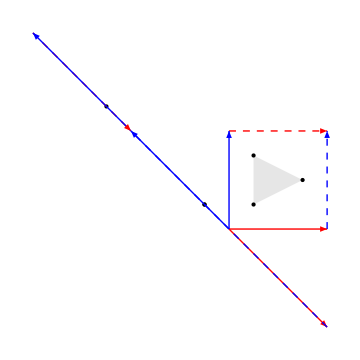
-Graphics- | Matrix | Determinant
(1 | -2
-1 | 2) | 0
Eigenvalues | Eigenvectors
3 | (-1
1)
0 | (2
1)

```mathematica
InitialA=({{1, -2}, {-1, 2}}); 
xrange={0,3}
yrange={0,3}
u=InitialA[[All,1]]
v=InitialA[[All,2]]
box=1
heart=0
Evec=0
circle=0
parabola=0
triangle=1
trianglepoints={{3/4,1/2},{1/4,3/4},{1/4,1/4}}

A=Transpose[{u,v}];
Evals=Eigenvalues[A];
Evecs=Eigenvectors[A];
 Grid[{{Show[Graphics[{ Thick, 
If[triangle==1,{
{GrayLevel[.9],Polygon[trianglepoints]},{GrayLevel[.9],Polygon[trianglepoints.Transpose[A]]},
PointSize[Large],
Point[trianglepoints.Transpose[A]],
Point[trianglepoints]
},Thick],
If[box==1,{
Red, Arrow[{{0, 0}, {1,0}}], {Dashed, Arrow[{{0,1}, {1,1}}]},
Blue, Arrow[{{0, 0}, {0,1}}], {Dashed, Arrow[{{1,0},{1,1}}]},
Red, Arrow[{{0, 0}, u}], {Dashed, Arrow[{v, u + v}]},
Blue, Arrow[{{0, 0}, v}], {Dashed, Arrow[{u, u + v}]}
},Thick],
If[Evec==1,{
Green,Arrow[{{0,0},Evals[[1]]*Normalize[Evecs[[1]]]}],
Green,Arrow[{{0,0},Evals[[2]]*Normalize[Evecs[[2]]]}],
Green,Arrow[{{0,0},-Evals[[1]]*Normalize[Evecs[[1]]]}],
Green,Arrow[{{0,0},-Evals[[2]]*Normalize[Evecs[[2]]]}],
Purple,Arrow[{{0,0},Normalize[Evecs[[1]]]}],
Purple,Arrow[{{0,0},Normalize[Evecs[[2]]]}],
Purple,Arrow[{{0,0},-Normalize[Evecs[[1]]]}],
Purple,Arrow[{{0,0},-Normalize[Evecs[[2]]]}]
},Thick]
}, Axes -> True,ImageSize->Medium],
If[parabola==1,
RegionPlot[Evaluate[(-u[[1]]-y)^2-4(u[[1]]*y-u[[2]]*x)<0],{x,-10,10},{y,-10,10},PlotStyle->Opacity[.1]]
,ParametricPlot[{0,0},{t,0,2Pi}]],
If[circle==1,
{ParametricPlot[A.{Cos[t],Sin[t]},{t,0,2Pi}],
ParametricPlot[{Cos[t],Sin[t]},{t,0,2Pi}]}
,ParametricPlot[{0,0},{t,0,2Pi}]],
If[heart==1,{ParametricPlot[1/3*({(1-Sin[t])*Cos[t],(1-Sin[t])*Sin[t]})*s+{1.5/3,2.5/3},{t,Pi/2,3Pi/2},{s,0,1},PlotStyle->{Pink,Opacity[.5]},Mesh->None],
ParametricPlot[A.(1/3*({(1-Sin[t])*Cos[t],(1-Sin[t])*Sin[t]})*s+{1.5/3,2.5/3}),{t,Pi/2,3Pi/2},{s,0,1},PlotStyle->{Pink,Opacity[.5]},Mesh->None],
ParametricPlot[1/3*({(1-Sin[t])*Cos[t],(1-Sin[t])*Sin[t]})*s+{1.5/3,2.5/3},{t,-Pi/2,Pi/2},{s,0,1},PlotStyle->{Purple,Opacity[.5]},Mesh->None],
ParametricPlot[A.(1/3*({(1-Sin[t])*Cos[t],(1-Sin[t])*Sin[t]})*s+{1.5/3,2.5/3}),{t,-Pi/2,Pi/2},{s,0,1},PlotStyle->{Purple,Opacity[.5]},Mesh->None]}
,ParametricPlot[{0,0},{t,0,2Pi}]],
 PlotRange -> All,Axes->False],
Grid[{{
"Matrix","Determinant"},
{{{Style[A[[1,1]],Red],Style[A[[1,2]],Blue]},{Style[A[[2,1]],Red],Style[A[[2,2]],Blue]}}//MatrixForm,Det[A]},
{"Eigenvalues","Eigenvectors"},
{Evals[[1]],Evecs[[1]]//MatrixForm},
{Evals[[2]],Evecs[[2]]//MatrixForm}
}]}}]
```

{0,3}

{0,3}

{1,-1}

{-2,2}

1

1

1

«1 more identical outputs»

0

0

{{3/4,1/2},{1/4,3/4},{1/4,1/4}}

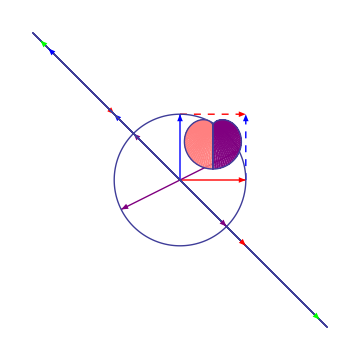
-Graphics- | Matrix | Determinant
(1 | -2
-1 | 2) | 0
Eigenvalues | Eigenvectors
3 | (-1
1)
0 | (2
1)

```mathematica
xrange={0,3}
yrange={0,3}
u=InitialA[[All,1]]
v=InitialA[[All,2]]
box=1
heart=1
Evec=1
circle=1
parabola=0
triangle=0
trianglepoints={{3/4,1/2},{1/4,3/4},{1/4,1/4}}

A=Transpose[{u,v}];
Evals=Eigenvalues[A];
Evecs=Eigenvectors[A];
 Grid[{{Show[Graphics[{ Thick, 
If[triangle==1,{
{GrayLevel[.9],Polygon[trianglepoints]},{GrayLevel[.9],Polygon[trianglepoints.Transpose[A]]},
PointSize[Large],
Point[trianglepoints.Transpose[A]],
Point[trianglepoints]
},Thick],
If[box==1,{
Red, Arrow[{{0, 0}, {1,0}}], {Dashed, Arrow[{{0,1}, {1,1}}]},
Blue, Arrow[{{0, 0}, {0,1}}], {Dashed, Arrow[{{1,0},{1,1}}]},
Red, Arrow[{{0, 0}, u}], {Dashed, Arrow[{v, u + v}]},
Blue, Arrow[{{0, 0}, v}], {Dashed, Arrow[{u, u + v}]}
},Thick],
If[Evec==1,{
Green,Arrow[{{0,0},Evals[[1]]*Normalize[Evecs[[1]]]}],
Green,Arrow[{{0,0},Evals[[2]]*Normalize[Evecs[[2]]]}],
Green,Arrow[{{0,0},-Evals[[1]]*Normalize[Evecs[[1]]]}],
Green,Arrow[{{0,0},-Evals[[2]]*Normalize[Evecs[[2]]]}],
Purple,Arrow[{{0,0},Normalize[Evecs[[1]]]}],
Purple,Arrow[{{0,0},Normalize[Evecs[[2]]]}],
Purple,Arrow[{{0,0},-Normalize[Evecs[[1]]]}],
Purple,Arrow[{{0,0},-Normalize[Evecs[[2]]]}]
},Thick]
}, Axes -> True,ImageSize->Medium],
If[parabola==1,
RegionPlot[Evaluate[(-u[[1]]-y)^2-4(u[[1]]*y-u[[2]]*x)<0],{x,-10,10},{y,-10,10},PlotStyle->Opacity[.1]]
,ParametricPlot[{0,0},{t,0,2Pi}]],
If[circle==1,
{ParametricPlot[A.{Cos[t],Sin[t]},{t,0,2Pi}],
ParametricPlot[{Cos[t],Sin[t]},{t,0,2Pi}]}
,ParametricPlot[{0,0},{t,0,2Pi}]],
If[heart==1,{ParametricPlot[1/3*({(1-Sin[t])*Cos[t],(1-Sin[t])*Sin[t]})*s+{1.5/3,2.5/3},{t,Pi/2,3Pi/2},{s,0,1},PlotStyle->{Pink,Opacity[.5]},Mesh->None],
ParametricPlot[A.(1/3*({(1-Sin[t])*Cos[t],(1-Sin[t])*Sin[t]})*s+{1.5/3,2.5/3}),{t,Pi/2,3Pi/2},{s,0,1},PlotStyle->{Pink,Opacity[.5]},Mesh->None],
ParametricPlot[1/3*({(1-Sin[t])*Cos[t],(1-Sin[t])*Sin[t]})*s+{1.5/3,2.5/3},{t,-Pi/2,Pi/2},{s,0,1},PlotStyle->{Purple,Opacity[.5]},Mesh->None],
ParametricPlot[A.(1/3*({(1-Sin[t])*Cos[t],(1-Sin[t])*Sin[t]})*s+{1.5/3,2.5/3}),{t,-Pi/2,Pi/2},{s,0,1},PlotStyle->{Purple,Opacity[.5]},Mesh->None]}
,ParametricPlot[{0,0},{t,0,2Pi}]],
 PlotRange -> All,Axes->False],
Grid[{{
"Matrix","Determinant"},
{{{Style[A[[1,1]],Red],Style[A[[1,2]],Blue]},{Style[A[[2,1]],Red],Style[A[[2,2]],Blue]}}//MatrixForm,Det[A]},
{"Eigenvalues","Eigenvectors"},
{Evals[[1]],Evecs[[1]]//MatrixForm},
{Evals[[2]],Evecs[[2]]//MatrixForm}
}]}}]
```

```mathematica
box=1
eigenvectors=0
sphere=0
flower=1

A=({{0, 1, -1}, {-1, 0, 1}, {1, -1, 0}});


u=A[[All,1]];
v=A[[All,2]];
w=A[[All,3]];

Evals=Eigenvalues[A];
Evecs=Eigenvectors[A]; 

ev1=Normalize[Evecs[[1]]];
ev2=Normalize[Evecs[[2]]];
ev3=Normalize[Evecs[[3]]];

z={0,0,0};
e1={1,0,0};
e2={0,1,0};
e3={0,0,1};

boxp=Show[{ Graphics3D[{ 
Thick, Red, Arrow[{z,e1}], {Dashed, Arrow[{e2, e2+e1}],Arrow[{e3, e3+e1}]},
Green, Arrow[{z,e2}], {Dashed, Arrow[{e1, e1+e2}],Arrow[{e3, e3+e2}]},
Blue, Arrow[{z,e3}], {Dashed, Arrow[{e1, e1+e3}],Arrow[{e2, e2+e3}]},
Red, Arrow[{z,u}], {Dashed, Arrow[{v, v+u}],Arrow[{w, w+u}]},
Green, Arrow[{z,v}], {Dashed, Arrow[{u, u+v}],Arrow[{w, w+v}]},
Blue, Arrow[{z,w}], {Dashed, Arrow[{u, u+w}],Arrow[{v, v+w}]}
}],
ParametricPlot3D[s*e1+t*e2,{s,0,1},{t,0,1},PlotStyle->{RGBColor[1,1,0],Opacity[.2]},Mesh->{1,1},MeshStyle->{Green,Red},MeshStyle->Opacity[.2]],
ParametricPlot3D[s*e1+t*e3,{s,0,1},{t,0,1},PlotStyle->{RGBColor[1,0,1],Opacity[.2]},Mesh->{1,1},MeshStyle->{Blue,Red},MeshStyle->Opacity[.2]],
ParametricPlot3D[s*e2+t*e3,{s,0,1},{t,0,1},PlotStyle->{RGBColor[0,1,1],Opacity[.2]},Mesh->{1,1},MeshStyle->{Blue,Green},MeshStyle->Opacity[.2]],

ParametricPlot3D[s*u+t*v,{s,0,1},{t,0,1},PlotStyle->{RGBColor[1,1,0],Opacity[.2]},Mesh->{1,1},MeshStyle->{Green,Red},MeshStyle->Opacity[.2]],
ParametricPlot3D[s*u+t*w,{s,0,1},{t,0,1},PlotStyle->{RGBColor[1,0,1],Opacity[.2]},Mesh->{1,1},MeshStyle->{Blue,Red},MeshStyle->Opacity[.2]],
ParametricPlot3D[s*v+t*w,{s,0,1},{t,0,1},PlotStyle->{RGBColor[0,1,1],Opacity[.2]},Mesh->{1,1},MeshStyle->{Blue,Green},MeshStyle->Opacity[.2]]
}];

evecp=Graphics3D[{ 
Thick, Black, 
Arrow[{z,ev1}],
Arrow[{z,ev2}],
Arrow[{z,ev3}],
Thick, Purple, 
Arrow[{z,Evals[[1]]*ev1}],
Arrow[{z,Evals[[2]]*ev2}],
Arrow[{z,Evals[[3]]*ev3}]
}];

p=ParametricPlot3D[1/2{Cos[t]Cos[s]Sin[3s],Sin[t]Cos[s]Sin[3s],Sin[s]Sin[3s]}+{1/2,1/2,1/2},{s,0,Pi},{t,0,2Pi},PerformanceGoal->"Speed",PlotStyle->Opacity[.5]];
Ap=ParametricPlot3D[A.(1/2{Cos[t]Cos[s]Sin[3s],Sin[t]Cos[s]Sin[3s],Sin[s]Sin[3s]}+{1/2,1/2,1/2}),{s,0,Pi},{t,0,2Pi},PerformanceGoal->"Speed",PlotStyle->Opacity[.5]];
sp=ParametricPlot3D[{Cos[t]Sin[s],Sin[t]Sin[s],Cos[s]},{s,0,Pi},{t,0,2Pi},PlotStyle->None,MeshStyle->Opacity[.2]];
Asp=ParametricPlot3D[A.{Cos[t]Sin[s],Sin[t]Sin[s],Cos[s]},{s,0,Pi},{t,0,2Pi},PlotStyle->None,MeshStyle->Opacity[.2]];


Grid[{{Show[{
If[box==1,boxp,Graphics3D[Point[{z}]]],
If[eigenvectors==1,evecp,Graphics3D[Point[{z}]]],
If[sphere==1,{sp,Asp},Graphics3D[Point[{z}]]],
If[flower==1,{p,Ap},Graphics3D[Point[{z}]]]
},Axes->True,AxesLabel->{"x","y","z"},ImageSize->Medium],
Grid[({{"Matrix", "Determinant"}, {A//MatrixForm, Det[A]}, {"Eigenvalue", "Eigenvector"}, {Evals[[1]], Evecs[[1]]//MatrixForm}, {Evals[[2]], Evecs[[2]]//MatrixForm}, {Evals[[3]], Evecs[[3]]//MatrixForm}})]}}]
```

1

0

0

1

-Graphics3D- | Matrix | Determinant
(0 | 1 | -1
-1 | 0 | 1
1 | -1 | 0) | 0
Eigenvalue | Eigenvector
ⅈ √3 | (-1/2+(ⅈ √3)/2
-1/2-(ⅈ √3)/2
1)
-ⅈ √3 | (-1/2-(ⅈ √3)/2
-1/2+(ⅈ √3)/2
1)
0 | (1
1
1)

```mathematica
box=1
eigenvectors=1
sphere=1
flower=0



u=A[[All,1]];
v=A[[All,2]];
w=A[[All,3]];

Evals=Eigenvalues[A];
Evecs=Eigenvectors[A]; 

ev1=Normalize[Evecs[[3]]];
ev2=Normalize[Evecs[[3]]];
ev3=Normalize[Evecs[[3]]];

z={0,0,0};
e1={1,0,0};
e2={0,1,0};
e3={0,0,1};

boxp=Show[{ Graphics3D[{ 
Thick, Red, Arrow[{z,e1}], {Dashed, Arrow[{e2, e2+e1}],Arrow[{e3, e3+e1}]},
Green, Arrow[{z,e2}], {Dashed, Arrow[{e1, e1+e2}],Arrow[{e3, e3+e2}]},
Blue, Arrow[{z,e3}], {Dashed, Arrow[{e1, e1+e3}],Arrow[{e2, e2+e3}]},
Red, Arrow[{z,u}], {Dashed, Arrow[{v, v+u}],Arrow[{w, w+u}]},
Green, Arrow[{z,v}], {Dashed, Arrow[{u, u+v}],Arrow[{w, w+v}]},
Blue, Arrow[{z,w}], {Dashed, Arrow[{u, u+w}],Arrow[{v, v+w}]}
}],
ParametricPlot3D[s*e1+t*e2,{s,0,1},{t,0,1},PlotStyle->{RGBColor[1,1,0],Opacity[.2]},Mesh->{1,1},MeshStyle->{Green,Red},MeshStyle->Opacity[.2]],
ParametricPlot3D[s*e1+t*e3,{s,0,1},{t,0,1},PlotStyle->{RGBColor[1,0,1],Opacity[.2]},Mesh->{1,1},MeshStyle->{Blue,Red},MeshStyle->Opacity[.2]],
ParametricPlot3D[s*e2+t*e3,{s,0,1},{t,0,1},PlotStyle->{RGBColor[0,1,1],Opacity[.2]},Mesh->{1,1},MeshStyle->{Blue,Green},MeshStyle->Opacity[.2]],

ParametricPlot3D[s*u+t*v,{s,0,1},{t,0,1},PlotStyle->{RGBColor[1,1,0],Opacity[.2]},Mesh->{1,1},MeshStyle->{Green,Red},MeshStyle->Opacity[.2]],
ParametricPlot3D[s*u+t*w,{s,0,1},{t,0,1},PlotStyle->{RGBColor[1,0,1],Opacity[.2]},Mesh->{1,1},MeshStyle->{Blue,Red},MeshStyle->Opacity[.2]],
ParametricPlot3D[s*v+t*w,{s,0,1},{t,0,1},PlotStyle->{RGBColor[0,1,1],Opacity[.2]},Mesh->{1,1},MeshStyle->{Blue,Green},MeshStyle->Opacity[.2]]
}];

evecp=Graphics3D[{ 
Thick, Black, 
Arrow[{z,ev1}],
Arrow[{z,ev2}],
Arrow[{z,ev3}],
Thick, Purple, 
Arrow[{z,Evals[[3]]*ev1}],
Arrow[{z,Evals[[3]]*ev2}],
Arrow[{z,Evals[[3]]*ev3}]
}];

p=ParametricPlot3D[1/2{Cos[t]Cos[s]Sin[3s],Sin[t]Cos[s]Sin[3s],Sin[s]Sin[3s]}+{1/2,1/2,1/2},{s,0,Pi},{t,0,2Pi},PerformanceGoal->"Speed",PlotStyle->Opacity[.5]];
Ap=ParametricPlot3D[A.(1/2{Cos[t]Cos[s]Sin[3s],Sin[t]Cos[s]Sin[3s],Sin[s]Sin[3s]}+{1/2,1/2,1/2}),{s,0,Pi},{t,0,2Pi},PerformanceGoal->"Speed",PlotStyle->Opacity[.5]];
sp=ParametricPlot3D[{Cos[t]Sin[s],Sin[t]Sin[s],Cos[s]},{s,0,Pi},{t,0,2Pi},PlotStyle->None,MeshStyle->Opacity[.2]];
Asp=ParametricPlot3D[A.{Cos[t]Sin[s],Sin[t]Sin[s],Cos[s]},{s,0,Pi},{t,0,2Pi},PlotStyle->None,MeshStyle->Opacity[.2]];


Grid[{{Show[{
If[box==1,boxp,Graphics3D[Point[{z}]]],
If[eigenvectors==1,evecp,Graphics3D[Point[{z}]]],
If[sphere==1,{sp,Asp},Graphics3D[Point[{z}]]],
If[flower==1,{p,Ap},Graphics3D[Point[{z}]]]
},Axes->True,AxesLabel->{"x","y","z"},ImageSize->Medium],
Grid[({{"Matrix", "Determinant"}, {A//MatrixForm, Det[A]}, {"Eigenvalue", "Eigenvector"}, {Evals[[1]], Evecs[[1]]//MatrixForm}, {Evals[[2]], Evecs[[2]]//MatrixForm}, {Evals[[3]], Evecs[[3]]//MatrixForm}})]}}]
```

1

1

1

0

-Graphics3D- | Matrix | Determinant
(0 | 1 | -1
-1 | 0 | 1
1 | -1 | 0) | 0
Eigenvalue | Eigenvector
ⅈ √3 | (-1/2+(ⅈ √3)/2
-1/2-(ⅈ √3)/2
1)
-ⅈ √3 | (-1/2-(ⅈ √3)/2
-1/2+(ⅈ √3)/2
1)
0 | (1
1
1)

```mathematica
TeXForm[A]
```

\left(
\begin{array}{ccc}
 0 & 1 & -1 \\
 -1 & 0 & 1 \\
 1 & -1 & 0
\end{array}
\right)

### 2D to 3D

```mathematica
box=1
eigenvectors=0
circle=1
heart=1

A=({{0, 1, 0}, {1, 0, 0}, {1, 1, 0}});


u=A[[All,1]];
v=A[[All,2]];
w=A[[All,3]];

Evals=Eigenvalues[A];
Evecs=Eigenvectors[A]; 

ev1=Normalize[Evecs[[1]]];
ev2=Normalize[Evecs[[2]]];
ev3=Normalize[Evecs[[3]]];

z={0,0,0};
e1={1,0,0};
e2={0,1,0};
e3={0,0,1};

boxp=Show[{ Graphics3D[{ 
Thick, Red, Arrow[{z,e1}], {Dashed, Arrow[{e2, e2+e1}]},
Green, Arrow[{z,e2}], {Dashed, Arrow[{e1, e1+e2}]},
Red, Arrow[{z,u}], {Dashed, Arrow[{v, v+u}],Arrow[{w, w+u}]},
Green, Arrow[{z,v}], {Dashed, Arrow[{u, u+v}],Arrow[{w, w+v}]},
Blue, Arrow[{z,w}], {Dashed, Arrow[{u, u+w}],Arrow[{v, v+w}]}
}],
ParametricPlot3D[s*e1+t*e2,{s,0,1},{t,0,1},PlotStyle->{RGBColor[1,1,0],Opacity[.2]},Mesh->{1,1},MeshStyle->{Green,Red},MeshStyle->Opacity[.2]],

ParametricPlot3D[s*u+t*v,{s,0,1},{t,0,1},PlotStyle->{RGBColor[1,1,0],Opacity[.2]},Mesh->{1,1},MeshStyle->{Green,Red},MeshStyle->Opacity[.2]]
}];

evecp=Graphics3D[{ 
Thick, Black, 
Arrow[{z,ev1}],
Arrow[{z,ev2}],
Arrow[{z,ev3}],
Thick, Purple, 
Arrow[{z,Evals[[1]]*ev1}],
Arrow[{z,Evals[[2]]*ev2}],
Arrow[{z,Evals[[3]]*ev3}]
}];
rr=1/3*({(1-Sin[t])*Cos[t],(1-Sin[t])*Sin[t],0})*s+{1.5/3,2.5/3,0};
p=ParametricPlot3D[rr,{s,0,1},{t,0,2Pi},PlotStyle->Opacity[.5],Mesh->None];
Ap=ParametricPlot3D[A.rr,{s,0,1},{t,0,2Pi},PlotStyle->Opacity[.5],Mesh->None];
sp=ParametricPlot3D[{Cos[t],Sin[t],0},{t,0,2Pi},MeshStyle->Thick];
Asp=ParametricPlot3D[A.{Cos[t],Sin[t],0},{t,0,2Pi},MeshStyle->Thick];


Grid[{{Show[{
If[box==1,boxp,Graphics3D[Point[{z}]]],
If[eigenvectors==1,evecp,Graphics3D[Point[{z}]]],
If[circle==1,{sp,Asp},Graphics3D[Point[{z}]]],
If[heart==1,{p,Ap},Graphics3D[Point[{z}]]]
},Axes->True,AxesLabel->{"x","y","z"},ImageSize->Medium],
Grid[({{"Matrix", "Determinant"}, {A//MatrixForm, Det[A]}, {"Eigenvalue", "Eigenvector"}, {Evals[[1]], Evecs[[1]]//MatrixForm}, {Evals[[2]], Evecs[[2]]//MatrixForm}, {Evals[[3]], Evecs[[3]]//MatrixForm}})]}}]
```

1

0

1

1

-Graphics3D- | Matrix | Determinant
(0 | 1 | 0
1 | 0 | 0
1 | 1 | 0) | 0
Eigenvalue | Eigenvector
-1 | (-1
1
0)
1 | (1
1
2)
0 | (0
0
1)

### 3D to 2D

```mathematica
box=1
eigenvectors=0
sphere=0
flower=1
A=({{-2, -1, -1}, {1, 2, -1}, {0, 0, 0}});



u=A[[All,1]];
v=A[[All,2]];
w=A[[All,3]];

Evals=Eigenvalues[A];
Evecs=Eigenvectors[A]; 

ev1=Normalize[Evecs[[1]]];
ev2=Normalize[Evecs[[2]]];
ev3=Normalize[Evecs[[3]]];

z={0,0,0};
e1={1,0,0};
e2={0,1,0};
e3={0,0,1};

boxp=Show[{ Graphics3D[{ 
Thick, Red, Arrow[{z,e1}], {Dashed, Arrow[{e2, e2+e1}],Arrow[{e3, e3+e1}]},
Green, Arrow[{z,e2}], {Dashed, Arrow[{e1, e1+e2}],Arrow[{e3, e3+e2}]},
Blue, Arrow[{z,e3}], {Dashed, Arrow[{e1, e1+e3}],Arrow[{e2, e2+e3}]},
Red, Arrow[{z,u}], {Dashed, Arrow[{v, v+u}],Arrow[{w, w+u}]},
Green, Arrow[{z,v}], {Dashed, Arrow[{u, u+v}],Arrow[{w, w+v}]},
Blue, Arrow[{z,w}], {Dashed, Arrow[{u, u+w}],Arrow[{v, v+w}]}
}],
ParametricPlot3D[s*e1+t*e2,{s,0,1},{t,0,1},PlotStyle->{RGBColor[1,1,0],Opacity[.2]},Mesh->{1,1},MeshStyle->{Green,Red},MeshStyle->Opacity[.2]],
ParametricPlot3D[s*e1+t*e3,{s,0,1},{t,0,1},PlotStyle->{RGBColor[1,0,1],Opacity[.2]},Mesh->{1,1},MeshStyle->{Blue,Red},MeshStyle->Opacity[.2]],
ParametricPlot3D[s*e2+t*e3,{s,0,1},{t,0,1},PlotStyle->{RGBColor[0,1,1],Opacity[.2]},Mesh->{1,1},MeshStyle->{Blue,Green},MeshStyle->Opacity[.2]],

ParametricPlot3D[s*u+t*v,{s,0,1},{t,0,1},PlotStyle->{RGBColor[1,1,0],Opacity[.2]},Mesh->{1,1},MeshStyle->{Green,Red},MeshStyle->Opacity[.2]],
ParametricPlot3D[s*u+t*w,{s,0,1},{t,0,1},PlotStyle->{RGBColor[1,0,1],Opacity[.2]},Mesh->{1,1},MeshStyle->{Blue,Red},MeshStyle->Opacity[.2]],
ParametricPlot3D[s*v+t*w,{s,0,1},{t,0,1},PlotStyle->{RGBColor[0,1,1],Opacity[.2]},Mesh->{1,1},MeshStyle->{Blue,Green},MeshStyle->Opacity[.2]]
}];

evecp=Graphics3D[{ 
Thick, Black, 
Arrow[{z,ev1}],
Arrow[{z,ev2}],
Arrow[{z,ev3}],
Thick, Purple, 
Arrow[{z,Evals[[1]]*ev1}],
Arrow[{z,Evals[[2]]*ev2}],
Arrow[{z,Evals[[3]]*ev3}]
}];

p=ParametricPlot3D[1/2{Cos[t]Cos[s]Sin[3s],Sin[t]Cos[s]Sin[3s],Sin[s]Sin[3s]}+{1/2,1/2,1/2},{s,0,Pi},{t,0,2Pi},PerformanceGoal->"Speed",PlotStyle->Opacity[.5]];
Ap=ParametricPlot3D[A.(1/2{Cos[t]Cos[s]Sin[3s],Sin[t]Cos[s]Sin[3s],Sin[s]Sin[3s]}+{1/2,1/2,1/2}),{s,0,Pi},{t,0,2Pi},PerformanceGoal->"Speed",PlotStyle->Opacity[.5]];
sp=ParametricPlot3D[{Cos[t]Sin[s],Sin[t]Sin[s],Cos[s]},{s,0,Pi},{t,0,2Pi},PlotStyle->None,MeshStyle->Opacity[.2]];
Asp=ParametricPlot3D[A.{Cos[t]Sin[s],Sin[t]Sin[s],Cos[s]},{s,0,Pi},{t,0,2Pi},PlotStyle->None,MeshStyle->Opacity[.2]];


Grid[{{Show[{
If[box==1,boxp,Graphics3D[Point[{z}]]],
If[eigenvectors==1,evecp,Graphics3D[Point[{z}]]],
If[sphere==1,{sp,Asp},Graphics3D[Point[{z}]]],
If[flower==1,{p,Ap},Graphics3D[Point[{z}]]]
},Axes->True,AxesLabel->{"x","y","z"},ImageSize->Medium],
Grid[({{"Matrix", "Determinant"}, {A//MatrixForm, Det[A]}, {"Eigenvalue", "Eigenvector"}, {Evals[[1]], Evecs[[1]]//MatrixForm}, {Evals[[2]], Evecs[[2]]//MatrixForm}, {Evals[[3]], Evecs[[3]]//MatrixForm}})]}}]
```

1

0

0

1

-Graphics3D- | Matrix | Determinant
(-2 | -1 | -1
1 | 2 | -1
0 | 0 | 0) | 0
Eigenvalue | Eigenvector
-√3 | (-2-√3
1
0)
√3 | (-2+√3
1
0)
0 | (-1
1
1)

```mathematica
box=1
eigenvectors=1
sphere=1
flower=0



u=A[[All,1]];
v=A[[All,2]];
w=A[[All,3]];

Evals=Eigenvalues[A];
Evecs=Eigenvectors[A]; 

ev1=Normalize[Evecs[[1]]];
ev2=Normalize[Evecs[[2]]];
ev3=Normalize[Evecs[[3]]];

z={0,0,0};
e1={1,0,0};
e2={0,1,0};
e3={0,0,1};

boxp=Show[{ Graphics3D[{ 
Thick, Red, Arrow[{z,e1}], {Dashed, Arrow[{e2, e2+e1}],Arrow[{e3, e3+e1}]},
Green, Arrow[{z,e2}], {Dashed, Arrow[{e1, e1+e2}],Arrow[{e3, e3+e2}]},
Blue, Arrow[{z,e3}], {Dashed, Arrow[{e1, e1+e3}],Arrow[{e2, e2+e3}]},
Red, Arrow[{z,u}], {Dashed, Arrow[{v, v+u}],Arrow[{w, w+u}]},
Green, Arrow[{z,v}], {Dashed, Arrow[{u, u+v}],Arrow[{w, w+v}]},
Blue, Arrow[{z,w}], {Dashed, Arrow[{u, u+w}],Arrow[{v, v+w}]}
}],
ParametricPlot3D[s*e1+t*e2,{s,0,1},{t,0,1},PlotStyle->{RGBColor[1,1,0],Opacity[.2]},Mesh->{1,1},MeshStyle->{Green,Red},MeshStyle->Opacity[.2]],
ParametricPlot3D[s*e1+t*e3,{s,0,1},{t,0,1},PlotStyle->{RGBColor[1,0,1],Opacity[.2]},Mesh->{1,1},MeshStyle->{Blue,Red},MeshStyle->Opacity[.2]],
ParametricPlot3D[s*e2+t*e3,{s,0,1},{t,0,1},PlotStyle->{RGBColor[0,1,1],Opacity[.2]},Mesh->{1,1},MeshStyle->{Blue,Green},MeshStyle->Opacity[.2]],

ParametricPlot3D[s*u+t*v,{s,0,1},{t,0,1},PlotStyle->{RGBColor[1,1,0],Opacity[.2]},Mesh->{1,1},MeshStyle->{Green,Red},MeshStyle->Opacity[.2]],
ParametricPlot3D[s*u+t*w,{s,0,1},{t,0,1},PlotStyle->{RGBColor[1,0,1],Opacity[.2]},Mesh->{1,1},MeshStyle->{Blue,Red},MeshStyle->Opacity[.2]],
ParametricPlot3D[s*v+t*w,{s,0,1},{t,0,1},PlotStyle->{RGBColor[0,1,1],Opacity[.2]},Mesh->{1,1},MeshStyle->{Blue,Green},MeshStyle->Opacity[.2]]
}];

evecp=Graphics3D[{ 
Thick, Black, 
Arrow[{z,ev1}],
Arrow[{z,ev2}],
Arrow[{z,ev3}],
Thick, Purple, 
Arrow[{z,Evals[[1]]*ev1}],
Arrow[{z,Evals[[2]]*ev2}],
Arrow[{z,Evals[[3]]*ev3}]
}];

p=ParametricPlot3D[1/2{Cos[t]Cos[s]Sin[3s],Sin[t]Cos[s]Sin[3s],Sin[s]Sin[3s]}+{1/2,1/2,1/2},{s,0,Pi},{t,0,2Pi},PerformanceGoal->"Speed",PlotStyle->Opacity[.5]];
Ap=ParametricPlot3D[A.(1/2{Cos[t]Cos[s]Sin[3s],Sin[t]Cos[s]Sin[3s],Sin[s]Sin[3s]}+{1/2,1/2,1/2}),{s,0,Pi},{t,0,2Pi},PerformanceGoal->"Speed",PlotStyle->Opacity[.5]];
sp=ParametricPlot3D[{Cos[t]Sin[s],Sin[t]Sin[s],Cos[s]},{s,0,Pi},{t,0,2Pi},PlotStyle->None,MeshStyle->Opacity[.2]];
Asp=ParametricPlot3D[A.{Cos[t]Sin[s],Sin[t]Sin[s],Cos[s]},{s,0,Pi},{t,0,2Pi},PlotStyle->None,MeshStyle->Opacity[.2]];


Grid[{{Show[{
If[box==1,boxp,Graphics3D[Point[{z}]]],
If[eigenvectors==1,evecp,Graphics3D[Point[{z}]]],
If[sphere==1,{sp,Asp},Graphics3D[Point[{z}]]],
If[flower==1,{p,Ap},Graphics3D[Point[{z}]]]
},Axes->True,AxesLabel->{"x","y","z"},ImageSize->Medium],
Grid[({{"Matrix", "Determinant"}, {A//MatrixForm, Det[A]}, {"Eigenvalue", "Eigenvector"}, {Evals[[1]], Evecs[[1]]//MatrixForm}, {Evals[[2]], Evecs[[2]]//MatrixForm}, {Evals[[3]], Evecs[[3]]//MatrixForm}})]}}]
```

1

1

1

0

-Graphics3D- | Matrix | Determinant
(-2 | -1 | -1
1 | 2 | -1
0 | 0 | 0) | 0
Eigenvalue | Eigenvector
-√3 | (-2-√3
1
0)
√3 | (-2+√3
1
0)
0 | (-1
1
1)

### Rotations

π/6

{0,3}

{0,3}

{(√3)/2,1/2}

{-1/2,(√3)/2}

1

0

0

0

«1 more identical outputs»

1

{{3/4,1/2},{1/4,3/4},{1/4,1/4}}

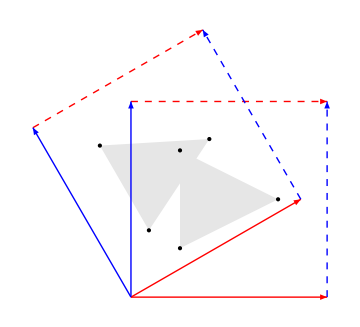
-Graphics- | Matrix | Determinant
((√3)/2 | -1/2
1/2 | (√3)/2) | 1
Eigenvalues | Eigenvectors
1/2 (ⅈ+√3) | (ⅈ
1)
1/2 (-ⅈ+√3) | (-ⅈ
1)

```mathematica
t=Pi/6
InitialA=({{Cos[t], -Sin[t]}, {Sin[t], Cos[t]}}); 
xrange={0,3}
yrange={0,3}
u=InitialA[[All,1]]
v=InitialA[[All,2]]
box=1
heart=0
Evec=0
circle=0
parabola=0
triangle=1
trianglepoints={{3/4,1/2},{1/4,3/4},{1/4,1/4}}

A=Transpose[{u,v}];
Evals=Eigenvalues[A];
Evecs=Eigenvectors[A];
 Grid[{{Show[Graphics[{ Thick, 
If[triangle==1,{
{GrayLevel[.9],Polygon[trianglepoints]},{GrayLevel[.9],Polygon[trianglepoints.Transpose[A]]},
PointSize[Large],
Point[trianglepoints.Transpose[A]],
Point[trianglepoints]
},Thick],
If[box==1,{
Red, Arrow[{{0, 0}, {1,0}}], {Dashed, Arrow[{{0,1}, {1,1}}]},
Blue, Arrow[{{0, 0}, {0,1}}], {Dashed, Arrow[{{1,0},{1,1}}]},
Red, Arrow[{{0, 0}, u}], {Dashed, Arrow[{v, u + v}]},
Blue, Arrow[{{0, 0}, v}], {Dashed, Arrow[{u, u + v}]}
},Thick],
If[Evec==1,{
Green,Arrow[{{0,0},Evals[[1]]*Normalize[Evecs[[1]]]}],
Green,Arrow[{{0,0},Evals[[2]]*Normalize[Evecs[[2]]]}],
Green,Arrow[{{0,0},-Evals[[1]]*Normalize[Evecs[[1]]]}],
Green,Arrow[{{0,0},-Evals[[2]]*Normalize[Evecs[[2]]]}],
Purple,Arrow[{{0,0},Normalize[Evecs[[1]]]}],
Purple,Arrow[{{0,0},Normalize[Evecs[[2]]]}],
Purple,Arrow[{{0,0},-Normalize[Evecs[[1]]]}],
Purple,Arrow[{{0,0},-Normalize[Evecs[[2]]]}]
},Thick]
}, Axes -> True,ImageSize->Medium],
If[parabola==1,
RegionPlot[Evaluate[(-u[[1]]-y)^2-4(u[[1]]*y-u[[2]]*x)<0],{x,-10,10},{y,-10,10},PlotStyle->Opacity[.1]]
,ParametricPlot[{0,0},{t,0,2Pi}]],
If[circle==1,
{ParametricPlot[A.{Cos[t],Sin[t]},{t,0,2Pi}],
ParametricPlot[{Cos[t],Sin[t]},{t,0,2Pi}]}
,ParametricPlot[{0,0},{t,0,2Pi}]],
If[heart==1,{ParametricPlot[1/3*({(1-Sin[t])*Cos[t],(1-Sin[t])*Sin[t]})*s+{1.5/3,2.5/3},{t,Pi/2,3Pi/2},{s,0,1},PlotStyle->{Pink,Opacity[.5]},Mesh->None],
ParametricPlot[A.(1/3*({(1-Sin[t])*Cos[t],(1-Sin[t])*Sin[t]})*s+{1.5/3,2.5/3}),{t,Pi/2,3Pi/2},{s,0,1},PlotStyle->{Pink,Opacity[.5]},Mesh->None],
ParametricPlot[1/3*({(1-Sin[t])*Cos[t],(1-Sin[t])*Sin[t]})*s+{1.5/3,2.5/3},{t,-Pi/2,Pi/2},{s,0,1},PlotStyle->{Purple,Opacity[.5]},Mesh->None],
ParametricPlot[A.(1/3*({(1-Sin[t])*Cos[t],(1-Sin[t])*Sin[t]})*s+{1.5/3,2.5/3}),{t,-Pi/2,Pi/2},{s,0,1},PlotStyle->{Purple,Opacity[.5]},Mesh->None]}
,ParametricPlot[{0,0},{t,0,2Pi}]],
 PlotRange -> All,Axes->False],
Grid[{{
"Matrix","Determinant"},
{{{Style[A[[1,1]],Red],Style[A[[1,2]],Blue]},{Style[A[[2,1]],Red],Style[A[[2,2]],Blue]}}//MatrixForm,Det[A]},
{"Eigenvalues","Eigenvectors"},
{Evals[[1]],Evecs[[1]]//MatrixForm},
{Evals[[2]],Evecs[[2]]//MatrixForm}
}]}}]
```

### Null space use

```mathematica
A=({{0, 1, 0, 2, 0, 0}, {0, 0, 1, -3, 0, 1}, {0, 0, 0, 0, 1, 4}, {0, 0, 0, 0, 0, 0}})
```

{{0,1,0,2,0,0},{0,0,1,-3,0,1},{0,0,0,0,1,4},{0,0,0,0,0,0}}

### Shadows

```mathematica
box=1
eigenvectors=0
sphere=0
flower=1
A=({{1, 0, -1/2}, {0, 1, -1/4}, {0, 0, 0}});



u=A[[All,1]];
v=A[[All,2]];
w=A[[All,3]];

Evals=Eigenvalues[A];
Evecs=Eigenvectors[A]; 

ev1=Normalize[Evecs[[1]]];
ev2=Normalize[Evecs[[2]]];
ev3=Normalize[Evecs[[3]]];

z={0,0,0};
e1={1,0,0};
e2={0,1,0};
e3={0,0,1};

boxp=Show[{ Graphics3D[{ 
Thick, Red, Arrow[{z,e1}], {Dashed, Arrow[{e2, e2+e1}],Arrow[{e3, e3+e1}]},
Green, Arrow[{z,e2}], {Dashed, Arrow[{e1, e1+e2}],Arrow[{e3, e3+e2}]},
Blue, Arrow[{z,e3}], {Dashed, Arrow[{e1, e1+e3}],Arrow[{e2, e2+e3}]},
Red, Arrow[{z,u}], {Dashed, Arrow[{v, v+u}],Arrow[{w, w+u}]},
Green, Arrow[{z,v}], {Dashed, Arrow[{u, u+v}],Arrow[{w, w+v}]},
Blue, Arrow[{z,w}], {Dashed, Arrow[{u, u+w}],Arrow[{v, v+w}]}
}],
ParametricPlot3D[s*e1+t*e2,{s,0,1},{t,0,1},PlotStyle->{RGBColor[1,1,0],Opacity[.2]},Mesh->{1,1},MeshStyle->{Green,Red},MeshStyle->Opacity[.2]],
ParametricPlot3D[s*e1+t*e3,{s,0,1},{t,0,1},PlotStyle->{RGBColor[1,0,1],Opacity[.2]},Mesh->{1,1},MeshStyle->{Blue,Red},MeshStyle->Opacity[.2]],
ParametricPlot3D[s*e2+t*e3,{s,0,1},{t,0,1},PlotStyle->{RGBColor[0,1,1],Opacity[.2]},Mesh->{1,1},MeshStyle->{Blue,Green},MeshStyle->Opacity[.2]],

ParametricPlot3D[s*u+t*v,{s,0,1},{t,0,1},PlotStyle->{RGBColor[1,1,0],Opacity[.2]},Mesh->{1,1},MeshStyle->{Green,Red},MeshStyle->Opacity[.2]],
ParametricPlot3D[s*u+t*w,{s,0,1},{t,0,1},PlotStyle->{RGBColor[1,0,1],Opacity[.2]},Mesh->{1,1},MeshStyle->{Blue,Red},MeshStyle->Opacity[.2]],
ParametricPlot3D[s*v+t*w,{s,0,1},{t,0,1},PlotStyle->{RGBColor[0,1,1],Opacity[.2]},Mesh->{1,1},MeshStyle->{Blue,Green},MeshStyle->Opacity[.2]]
}];

evecp=Graphics3D[{ 
Thick, Black, 
Arrow[{z,ev1}],
Arrow[{z,ev2}],
Arrow[{z,ev3}],
Thick, Purple, 
Arrow[{z,Evals[[1]]*ev1}],
Arrow[{z,Evals[[2]]*ev2}],
Arrow[{z,Evals[[3]]*ev3}]
}];

p=ParametricPlot3D[1/2{Cos[t]Cos[s]Sin[3s],Sin[t]Cos[s]Sin[3s],Sin[s]Sin[3s]}+{1/2,1/2,1/2},{s,0,Pi},{t,0,2Pi},PerformanceGoal->"Speed",PlotStyle->Opacity[.5]];
Ap=ParametricPlot3D[A.(1/2{Cos[t]Cos[s]Sin[3s],Sin[t]Cos[s]Sin[3s],Sin[s]Sin[3s]}+{1/2,1/2,1/2}),{s,0,Pi},{t,0,2Pi},PerformanceGoal->"Speed",PlotStyle->Opacity[.5]];
sp=ParametricPlot3D[{Cos[t]Sin[s],Sin[t]Sin[s],Cos[s]},{s,0,Pi},{t,0,2Pi},PlotStyle->None,MeshStyle->Opacity[.2]];
Asp=ParametricPlot3D[A.{Cos[t]Sin[s],Sin[t]Sin[s],Cos[s]},{s,0,Pi},{t,0,2Pi},PlotStyle->None,MeshStyle->Opacity[.2]];


Grid[{{Show[{
If[box==1,boxp,Graphics3D[Point[{z}]]],
If[eigenvectors==1,evecp,Graphics3D[Point[{z}]]],
If[sphere==1,{sp,Asp},Graphics3D[Point[{z}]]],
If[flower==1,{p,Ap},Graphics3D[Point[{z}]]]
},Axes->True,AxesLabel->{"x","y","z"},ImageSize->Medium],
Grid[({{"Matrix", "Determinant"}, {A//MatrixForm, Det[A]}, {"Eigenvalue", "Eigenvector"}, {Evals[[1]], Evecs[[1]]//MatrixForm}, {Evals[[2]], Evecs[[2]]//MatrixForm}, {Evals[[3]], Evecs[[3]]//MatrixForm}})]}}]
```

1

0

0

1

-Graphics3D- | Matrix | Determinant
(1 | 0 | -1/2
0 | 1 | -1/4
0 | 0 | 0) | 0
Eigenvalue | Eigenvector
1 | (0
1
0)
1 | (1
0
0)
0 | (1/2
1/4
1)

```mathematica
box=1
eigenvectors=0
sphere=0
flower=1
A=({{2, 0, -1}, {0, 4, -1}, {0, 0, 0}});



u=A[[All,1]];
v=A[[All,2]];
w=A[[All,3]];

Evals=Eigenvalues[A];
Evecs=Eigenvectors[A]; 

ev1=Normalize[Evecs[[1]]];
ev2=Normalize[Evecs[[2]]];
ev3=Normalize[Evecs[[3]]];

z={0,0,0};
e1={1,0,0};
e2={0,1,0};
e3={0,0,1};

boxp=Show[{ Graphics3D[{ 
Thick, Red, Arrow[{z,e1}], {Dashed, Arrow[{e2, e2+e1}],Arrow[{e3, e3+e1}]},
Green, Arrow[{z,e2}], {Dashed, Arrow[{e1, e1+e2}],Arrow[{e3, e3+e2}]},
Blue, Arrow[{z,e3}], {Dashed, Arrow[{e1, e1+e3}],Arrow[{e2, e2+e3}]},
Red, Arrow[{z,u}], {Dashed, Arrow[{v, v+u}],Arrow[{w, w+u}]},
Green, Arrow[{z,v}], {Dashed, Arrow[{u, u+v}],Arrow[{w, w+v}]},
Blue, Arrow[{z,w}], {Dashed, Arrow[{u, u+w}],Arrow[{v, v+w}]}
}],
ParametricPlot3D[s*e1+t*e2,{s,0,1},{t,0,1},PlotStyle->{RGBColor[1,1,0],Opacity[.2]},Mesh->{1,1},MeshStyle->{Green,Red},MeshStyle->Opacity[.2]],
ParametricPlot3D[s*e1+t*e3,{s,0,1},{t,0,1},PlotStyle->{RGBColor[1,0,1],Opacity[.2]},Mesh->{1,1},MeshStyle->{Blue,Red},MeshStyle->Opacity[.2]],
ParametricPlot3D[s*e2+t*e3,{s,0,1},{t,0,1},PlotStyle->{RGBColor[0,1,1],Opacity[.2]},Mesh->{1,1},MeshStyle->{Blue,Green},MeshStyle->Opacity[.2]],

ParametricPlot3D[s*u+t*v,{s,0,1},{t,0,1},PlotStyle->{RGBColor[1,1,0],Opacity[.2]},Mesh->{1,1},MeshStyle->{Green,Red},MeshStyle->Opacity[.2]],
ParametricPlot3D[s*u+t*w,{s,0,1},{t,0,1},PlotStyle->{RGBColor[1,0,1],Opacity[.2]},Mesh->{1,1},MeshStyle->{Blue,Red},MeshStyle->Opacity[.2]],
ParametricPlot3D[s*v+t*w,{s,0,1},{t,0,1},PlotStyle->{RGBColor[0,1,1],Opacity[.2]},Mesh->{1,1},MeshStyle->{Blue,Green},MeshStyle->Opacity[.2]]
}];

evecp=Graphics3D[{ 
Thick, Black, 
Arrow[{z,ev1}],
Arrow[{z,ev2}],
Arrow[{z,ev3}],
Thick, Purple, 
Arrow[{z,Evals[[1]]*ev1}],
Arrow[{z,Evals[[2]]*ev2}],
Arrow[{z,Evals[[3]]*ev3}]
}];

p=ParametricPlot3D[1/2{Cos[t]Cos[s]Sin[3s],Sin[t]Cos[s]Sin[3s],Sin[s]Sin[3s]}+{1/2,1/2,1/2},{s,0,Pi},{t,0,2Pi},PerformanceGoal->"Speed",PlotStyle->Opacity[.5]];
Ap=ParametricPlot3D[A.(1/2{Cos[t]Cos[s]Sin[3s],Sin[t]Cos[s]Sin[3s],Sin[s]Sin[3s]}+{1/2,1/2,1/2}),{s,0,Pi},{t,0,2Pi},PerformanceGoal->"Speed",PlotStyle->Opacity[.5]];
sp=ParametricPlot3D[{Cos[t]Sin[s],Sin[t]Sin[s],Cos[s]},{s,0,Pi},{t,0,2Pi},PlotStyle->None,MeshStyle->Opacity[.2]];
Asp=ParametricPlot3D[A.{Cos[t]Sin[s],Sin[t]Sin[s],Cos[s]},{s,0,Pi},{t,0,2Pi},PlotStyle->None,MeshStyle->Opacity[.2]];


Grid[{{Show[{
If[box==1,boxp,Graphics3D[Point[{z}]]],
If[eigenvectors==1,evecp,Graphics3D[Point[{z}]]],
If[sphere==1,{sp,Asp},Graphics3D[Point[{z}]]],
If[flower==1,{p,Ap},Graphics3D[Point[{z}]]]
},Axes->True,AxesLabel->{"x","y","z"},ImageSize->Medium],
Grid[({{"Matrix", "Determinant"}, {A//MatrixForm, Det[A]}, {"Eigenvalue", "Eigenvector"}, {Evals[[1]], Evecs[[1]]//MatrixForm}, {Evals[[2]], Evecs[[2]]//MatrixForm}, {Evals[[3]], Evecs[[3]]//MatrixForm}})]}}]
```

1

0

0

1

-Graphics3D- | Matrix | Determinant
(2 | 0 | -1
0 | 4 | -1
0 | 0 | 0) | 0
Eigenvalue | Eigenvector
4 | (0
1
0)
2 | (1
0
0)
0 | (2
1
4)